```mathematica
aDay1 = {"12.122.129.170"->"12.123.30.110","12.122.129.170"->"12.123.30.250","12.122.254.41"->"12.122.129.170","12.123.30.110"->"12.123.30.5","12.123.30.250"->"12.123.30.5","12.123.30.5"->"208.174.194.65","12.129.193.235"->"12.129.193.236","12.129.193.236"->"12.129.193.253","12.129.193.253"->"12.122.254.41","204.70.196.245"->"216.113.122.77","204.70.198.5"->"204.70.196.245","207.253.253.138"->"[FW]","208.174.194.65"->"204.70.198.5","216.113.122.77"->"207.253.253.138"};
aDay2 = {"12.122.128.6"->"12.123.30.250","12.122.129.170"->"12.123.30.110","12.122.129.170"->"12.123.30.250","12.122.254.41"->"12.122.128.6","12.122.255.69"->"12.122.129.170","12.123.30.110"->"12.123.30.133","12.123.30.133"->"208.174.194.65","12.123.30.250"->"12.123.30.133","12.123.30.250"->"12.123.30.5","12.123.30.5"->"208.174.194.65","12.129.193.235"->"12.129.193.236","12.129.193.236"->"12.129.193.253","12.129.193.253"->"12.122.254.41","12.129.193.253"->"12.122.255.69","204.70.196.245"->"216.113.122.77","204.70.198.5"->"204.70.196.245","207.253.253.138"->"[FW]","208.174.194.65"->"204.70.198.5","216.113.122.77"->"207.253.253.138"};
aDay3 = {"12.122.128.6"->"12.123.30.110","12.122.129.170"->"12.123.30.110","12.122.254.41"->"12.122.128.6","12.122.255.69"->"12.122.129.170","12.123.30.110"->"12.123.30.133","12.123.30.110"->"12.123.30.5","12.123.30.133"->"208.174.194.65","12.123.30.5"->"208.174.194.65","12.129.193.235"->"12.129.193.236","12.129.193.236"->"12.129.193.253","12.129.193.253"->"12.122.254.41","12.129.193.253"->"12.122.255.69","204.70.196.245"->"216.113.122.77","204.70.198.5"->"204.70.196.245","207.253.253.138"->"[FW]","208.174.194.65"->"204.70.198.5","216.113.122.77"->"207.253.253.138"};
aDay4 = {"12.122.128.6"->"12.123.30.110","12.122.129.170"->"12.123.30.250","12.122.254.41"->"12.122.129.170","12.122.255.69"->"12.122.128.6","12.123.30.110"->"12.123.30.5","12.123.30.250"->"12.123.30.5","12.123.30.5"->"208.174.194.65","12.129.193.235"->"12.129.193.236","12.129.193.236"->"12.129.193.253","12.129.193.253"->"12.122.254.41","12.129.193.253"->"12.122.255.69","204.70.196.245"->"216.113.122.77","204.70.198.5"->"204.70.196.245","207.253.253.138"->"[FW]","208.174.194.65"->"204.70.198.5","216.113.122.77"->"207.253.253.138"};
aAllDays={"12.122.128.6"->"12.123.30.110","12.122.128.6"->"12.123.30.250","12.122.129.170"->"12.123.30.110","12.122.129.170"->"12.123.30.250","12.122.254.41"->"12.122.128.6","12.122.254.41"->"12.122.129.170","12.122.255.69"->"12.122.128.6","12.122.255.69"->"12.122.129.170","12.123.30.110"->"12.123.30.133","12.123.30.110"->"12.123.30.5","12.123.30.133"->"208.174.194.65","12.123.30.250"->"12.123.30.133","12.123.30.250"->"12.123.30.5","12.123.30.5"->"208.174.194.65","12.129.193.235"->"12.129.193.236","12.129.193.236"->"12.129.193.253","12.129.193.253"->"12.122.254.41","12.129.193.253"->"12.122.255.69","204.70.196.245"->"216.113.122.77","204.70.198.5"->"204.70.196.245","207.253.253.138"->"[FW]","208.174.194.65"->"204.70.198.5","216.113.122.77"->"207.253.253.138"};
```

```mathematica
TreePlot[aDay1,Automatic,"12.129.193.235",VertexLabeling->True,PlotRangePadding->0]
TreePlot[aDay2,Automatic,"12.129.193.235",VertexLabeling->True,PlotRangePadding->0]
TreePlot[aDay3,Automatic,"12.129.193.235",VertexLabeling->True,PlotRangePadding->0]
TreePlot[aDay4,Automatic,"12.129.193.235",VertexLabeling->True,PlotRangePadding->0]
TreePlot[aAllDays,Automatic,"12.129.193.235",VertexLabeling->True,PlotRangePadding->0]
```

```mathematica
bAllDays={"12.122.128.6"->"12.123.30.110","12.122.128.6"->"12.123.30.250","12.122.129.170"->"12.123.30.110","12.122.129.170"->"12.123.30.250","12.122.129.25"->"12.122.255.74","12.122.254.41"->"12.122.128.6","12.122.254.41"->"12.122.129.170","12.122.255.69"->"12.122.128.6","12.122.255.69"->"12.122.129.170","12.122.255.74"->"12.129.193.242","12.122.255.74"->"12.129.193.246","12.122.30.25"->"12.122.30.30","12.122.30.30"->"12.123.30.249","12.122.31.85"->"12.122.30.25","12.122.81.18"->"12.122.31.85","12.123.30.110"->"12.123.30.133","12.123.30.110"->"12.123.30.5","12.123.30.133"->"208.174.194.65","12.123.30.249"->"12.122.129.25","12.123.30.250"->"12.123.30.133","12.123.30.250"->"12.123.30.5","12.123.30.5"->"208.174.194.65","12.129.193.235"->"12.129.193.236","12.129.193.236"->"12.129.193.253","12.129.193.242"->"[NR]","12.129.193.242"->"12.129.193.235","12.129.193.246"->"[NR]","12.129.193.246"->"12.129.193.235","12.129.193.253"->"12.122.254.41","12.129.193.253"->"12.122.255.69","144.232.26.69"->"144.232.3.136","144.232.3.136"->"144.232.8.186","144.232.8.186"->"192.205.37.89","192.205.37.89"->"12.122.81.18","204.70.196.245"->"216.113.122.77","204.70.198.5"->"204.70.196.245","207.253.253.138"->"[FW]","207.253.253.160"->"216.113.122.74","208.174.194.65"->"204.70.198.5","216.113.10.49"->"207.253.253.160","216.113.122.74"->"144.232.26.69","216.113.122.77"->"207.253.253.138"};
```

```mathematica
TreePlot[bAllDays,Automatic,"12.129.193.235",VertexLabeling->True,PlotRangePadding->0]
```

```mathematica
cAllDays={"12.118.100.21"->"12.122.131.118","12.118.34.30"->"[FW]","12.122.1.2"->"12.122.2.53","12.122.1.209"->"12.122.28.158","12.122.1.210"->"12.122.28.178","12.122.1.5"->"12.122.28.157","12.122.1.6"->"12.122.143.69","12.122.128.101"->"192.205.35.194","12.122.128.105"->"192.205.34.14","12.122.128.13"->"192.205.33.226","12.122.128.14"->"12.123.30.109","12.122.128.170"->"12.123.30.110","12.122.128.2"->"12.123.30.110","12.122.128.2"->"12.123.30.250","12.122.128.25"->"12.122.255.74","12.122.128.25"->"12.129.193.246","12.122.128.26"->"12.123.30.110","12.122.128.6"->"12.123.30.110","12.122.128.6"->"12.123.30.250","12.122.128.9"->"192.205.33.226","12.122.129.10"->"12.123.30.249","12.122.129.101"->"192.205.34.14","12.122.129.106"->"12.123.30.249","12.122.129.13"->"192.205.33.226","12.122.129.170"->"12.123.30.110","12.122.129.170"->"12.123.30.250","12.122.129.2"->"12.123.30.250","12.122.129.25"->"12.122.255.74","12.122.129.25"->"12.129.193.242","12.122.129.25"->"12.129.193.246","12.122.129.26"->"12.123.30.110","12.122.129.26"->"12.123.30.250","12.122.129.29"->"192.205.35.130","12.122.129.6"->"12.123.30.110","12.122.129.6"->"12.123.30.250","12.122.129.61"->"192.205.34.134","12.122.129.9"->"192.205.33.226","12.122.131.118"->"12.122.1.2","12.122.131.22"->"12.122.1.2","12.122.135.10"->"12.122.4.53","12.122.135.129"->"[FW]","12.122.135.14"->"12.122.4.53","12.122.137.150"->"12.122.3.122","12.122.138.22"->"12.122.28.178","12.122.143.69"->"12.88.228.14","12.122.143.70"->"12.122.1.5","12.122.146.77"->"12.118.34.30","12.122.2.125"->"12.122.2.205","12.122.2.126"->"12.122.2.210","12.122.2.205"->"[FW]","12.122.2.205"->"12.122.31.85","12.122.2.206"->"12.122.2.126","12.122.2.209"->"[NR]","12.122.2.209"->"12.122.2.125","12.122.2.210"->"12.122.4.54","12.122.2.53"->"12.122.31.85","12.122.254.41"->"12.122.128.170","12.122.254.41"->"12.122.128.2","12.122.254.41"->"12.122.128.6","12.122.254.41"->"12.122.129.170","12.122.254.41"->"12.122.129.2","12.122.254.65"->"12.122.128.2","12.122.254.65"->"12.122.128.26","12.122.254.65"->"12.122.128.6","12.122.254.65"->"12.122.129.2","12.122.254.65"->"12.122.129.26","12.122.254.65"->"12.122.129.6","12.122.255.69"->"12.122.128.170","12.122.255.69"->"12.122.128.2","12.122.255.69"->"12.122.128.6","12.122.255.69"->"12.122.129.170","12.122.255.69"->"12.122.129.2","12.122.255.73"->"12.122.128.2","12.122.255.73"->"12.122.128.26","12.122.255.73"->"12.122.128.6","12.122.255.73"->"12.122.129.2","12.122.255.73"->"12.122.129.26","12.122.255.73"->"12.122.129.6","12.122.255.74"->"[NR]","12.122.255.74"->"12.129.193.235","12.122.255.74"->"12.129.193.242","12.122.255.74"->"12.129.193.246","12.122.28.157"->"12.122.1.210","12.122.28.158"->"12.122.1.6","12.122.28.177"->"12.122.1.209","12.122.28.178"->"12.123.30.249","12.122.3.122"->"12.123.30.109","12.122.30.25"->"[FW]","12.122.30.25"->"12.122.30.30","12.122.30.26"->"12.122.31.86","12.122.30.29"->"12.122.30.26","12.122.30.30"->"12.123.30.249","12.122.31.134"->"12.122.31.193","12.122.31.193"->"12.122.146.77","12.122.31.85"->"12.122.30.25","12.122.31.86"->"12.122.2.206","12.122.4.53"->"[FW]","12.122.4.53"->"12.122.2.209","12.122.4.54"->"12.122.135.129","12.122.80.226"->"12.122.1.2","12.122.81.18"->"12.122.31.85","12.122.82.222"->"12.122.4.53","12.122.84.201"->"192.205.35.6","12.122.84.201"->"192.205.37.158","12.122.84.202"->"12.123.30.109","12.122.84.202"->"12.123.30.249","12.122.84.217"->"192.205.35.6","12.122.84.217"->"192.205.37.158","12.122.84.218"->"12.122.84.202","12.122.84.218"->"12.123.30.109","12.122.88.174"->"12.122.4.53","12.123.30.109"->"12.122.128.25","12.123.30.109"->"12.122.129.25","12.123.30.109"->"12.122.255.74","12.123.30.110"->"[NR]","12.123.30.110"->"12.122.128.101","12.123.30.110"->"12.122.128.105","12.123.30.110"->"12.122.128.13","12.123.30.110"->"12.122.128.9","12.123.30.110"->"12.122.129.101","12.123.30.110"->"12.122.129.9","12.123.30.110"->"12.122.84.201","12.123.30.110"->"12.122.84.217","12.123.30.110"->"12.123.30.133","12.123.30.110"->"12.123.30.17","12.123.30.110"->"12.123.30.189","12.123.30.110"->"12.123.30.5","12.123.30.133"->"208.174.194.65","12.123.30.17"->"77.67.79.173","12.123.30.189"->"77.67.79.173","12.123.30.249"->"[FW]","12.123.30.249"->"12.122.128.25","12.123.30.249"->"12.122.129.25","12.123.30.249"->"12.122.255.74","12.123.30.250"->"12.122.128.105","12.123.30.250"->"12.122.128.9","12.123.30.250"->"12.122.129.101","12.123.30.250"->"12.122.129.13","12.123.30.250"->"12.122.129.29","12.123.30.250"->"12.122.129.61","12.123.30.250"->"12.122.129.9","12.123.30.250"->"12.122.28.177","12.123.30.250"->"12.122.30.29","12.123.30.250"->"12.122.31.134","12.123.30.250"->"12.122.84.201","12.123.30.250"->"12.122.84.217","12.123.30.250"->"12.123.30.133","12.123.30.250"->"12.123.30.17","12.123.30.250"->"12.123.30.189","12.123.30.250"->"12.123.30.5","12.123.30.5"->"208.174.194.65","12.129.193.235"->"12.129.193.236","12.129.193.235"->"154.11.98.17","12.129.193.235"->"164.128.251.1","12.129.193.235"->"196.25.9.45","12.129.193.235"->"203.202.125.3","12.129.193.235"->"212.241.174.5","12.129.193.235"->"213.192.191.81","12.129.193.235"->"213.200.64.93","12.129.193.235"->"216.113.10.49","12.129.193.235"->"216.18.63.213","12.129.193.235"->"216.191.14.249","12.129.193.235"->"62.48.45.130","12.129.193.235"->"64.135.5.57","12.129.193.235"->"66.162.47.57","12.129.193.235"->"66.209.87.105","12.129.193.235"->"86.55.0.49","12.129.193.236"->"12.129.193.241","12.129.193.236"->"12.129.193.253","12.129.193.241"->"12.122.254.65","12.129.193.241"->"12.122.255.73","12.129.193.242"->"[FW]","12.129.193.242"->"[NR]","12.129.193.242"->"12.129.193.235","12.129.193.246"->"[FW]","12.129.193.246"->"[NR]","12.129.193.246"->"12.129.193.235","12.129.193.253"->"12.122.254.41","12.129.193.253"->"12.122.255.69","12.88.228.13"->"12.122.143.70","12.88.228.14"->"64.135.0.42","130.117.50.89"->"154.54.5.234","130.117.50.90"->"12.122.84.202","130.117.50.90"->"12.122.84.218","130.117.50.90"->"192.205.35.5","130.117.50.90"->"192.205.37.157","138.187.129.137"->"138.187.130.160","138.187.130.160"->"138.187.159.22","138.187.130.161"->"138.187.157.34","138.187.157.34"->"[NR]","138.187.157.34"->"164.128.251.50","138.187.157.5"->"138.187.129.137","138.187.159.21"->"138.187.130.161","138.187.159.22"->"198.32.118.79","138.187.159.22"->"213.248.96.101","144.232.13.43"->"144.232.4.83","144.232.13.50"->"216.113.122.81","144.232.18.123"->"144.232.20.44","144.232.18.123"->"144.232.9.167","144.232.20.44"->"213.206.129.123","144.232.20.74"->"144.232.9.110","144.232.24.13"->"80.77.64.34","144.232.24.211"->"144.232.9.167","144.232.26.11"->"144.232.18.123","144.232.26.11"->"144.232.24.211","144.232.26.11"->"144.232.9.148","144.232.26.11"->"144.232.9.157","144.232.26.69"->"144.232.3.136","144.232.26.69"->"144.232.9.148","144.232.3.136"->"144.232.8.186","144.232.3.213"->"144.232.4.83","144.232.3.213"->"144.232.4.97","144.232.3.213"->"144.232.4.99","144.232.3.215"->"144.232.4.83","144.232.4.83"->"144.232.9.74","144.232.4.83"->"144.232.9.78","144.232.4.85"->"144.232.4.97","144.232.4.87"->"144.232.4.83","144.232.4.89"->"144.232.4.83","144.232.4.91"->"144.232.4.83","144.232.4.91"->"144.232.4.97","144.232.4.97"->"144.232.9.74","144.232.4.97"->"144.232.9.78","144.232.4.99"->"144.232.9.74","144.232.8.186"->"192.205.37.89","144.232.9.110"->"144.232.24.13","144.232.9.148"->"144.232.20.74","144.232.9.148"->"144.232.9.167","144.232.9.157"->"144.232.20.44","144.232.9.157"->"144.232.9.167","144.232.9.166"->"144.232.13.43","144.232.9.166"->"144.232.13.50","144.232.9.166"->"144.232.3.213","144.232.9.166"->"144.232.3.215","144.232.9.166"->"144.232.4.85","144.232.9.166"->"144.232.4.87","144.232.9.166"->"144.232.4.89","144.232.9.166"->"144.232.4.91","144.232.9.167"->"213.206.129.123","144.232.9.167"->"217.118.224.54","144.232.9.74"->"12.122.80.226","144.232.9.78"->"12.122.80.226","154.11.10.217"->"[NR]","154.11.10.217"->"154.11.98.18","154.11.11.246"->"216.113.37.9","154.11.11.30"->"173.182.200.2","154.11.2.53"->"154.11.10.217","154.11.98.17"->"154.11.11.246","154.11.98.17"->"154.11.11.30","154.54.0.174"->"154.11.2.53","154.54.0.205"->"154.54.3.186","154.54.0.205"->"154.54.5.138","154.54.2.229"->"154.54.3.186","154.54.2.229"->"154.54.5.138","154.54.25.209"->"154.54.5.138","154.54.29.21"->"154.54.30.101","154.54.29.21"->"154.54.6.214","154.54.29.21"->"66.28.4.33","154.54.3.138"->"154.54.7.174","154.54.3.186"->"130.117.50.90","154.54.3.186"->"192.205.35.5","154.54.3.194"->"154.54.7.174","154.54.30.101"->"154.54.0.205","154.54.30.101"->"154.54.2.229","154.54.30.193"->"154.54.3.138","154.54.30.197"->"154.54.3.194","154.54.30.197"->"154.54.5.234","154.54.5.1"->"154.54.6.214","154.54.5.1"->"66.28.4.33","154.54.5.138"->"130.117.50.90","154.54.5.138"->"154.54.3.186","154.54.5.234"->"154.54.7.174","154.54.6.201"->"154.54.2.229","154.54.6.209"->"154.54.30.101","154.54.6.209"->"154.54.6.201","154.54.6.209"->"154.54.6.214","154.54.6.209"->"66.28.4.33","154.54.6.214"->"154.54.2.229","154.54.6.214"->"154.54.25.209","154.54.6.229"->"154.54.3.138","154.54.6.229"->"154.54.3.194","154.54.6.229"->"154.54.5.234","154.54.7.174"->"154.54.0.174","154.54.7.174"->"66.28.4.50","164.128.251.1"->"138.187.157.5","166.63.221.193"->"195.2.25.221","166.63.221.193"->"195.2.25.89","173.182.200.2"->"154.54.29.21","173.182.200.2"->"154.54.5.1","173.182.200.2"->"154.54.6.209","192.205.33.225"->"12.122.128.14","192.205.33.225"->"12.122.129.10","192.205.33.226"->"4.69.144.114","192.205.33.226"->"4.69.144.116","192.205.33.226"->"4.69.144.137","192.205.33.226"->"4.69.144.178","192.205.33.226"->"4.69.144.180","192.205.33.226"->"4.69.144.201","192.205.33.226"->"4.69.144.242","192.205.33.226"->"4.69.144.244","192.205.33.226"->"4.69.144.50","192.205.33.226"->"4.69.144.52","192.205.33.226"->"4.69.144.9","192.205.33.229"->"12.122.128.14","192.205.33.229"->"12.122.129.10","192.205.34.134"->"69.31.111.205","192.205.34.14"->"80.91.252.162","192.205.34.209"->"[FW]","192.205.34.209"->"12.122.135.10","192.205.34.209"->"12.122.135.14","192.205.34.53"->"12.122.131.22","192.205.35.130"->"216.6.12.30","192.205.35.194"->"66.192.245.68","192.205.35.5"->"12.122.84.202","192.205.35.5"->"12.122.84.218","192.205.35.5"->"12.123.30.109","192.205.35.5"->"192.205.37.157","192.205.35.6"->"130.117.50.89","192.205.35.6"->"154.54.30.197","192.205.35.6"->"154.54.6.229","192.205.36.121"->"12.122.137.150","192.205.36.137"->"[NR]","192.205.36.137"->"12.122.82.222","192.205.36.205"->"12.122.81.18","192.205.36.241"->"12.122.81.18","192.205.37.157"->"12.122.84.202","192.205.37.157"->"12.122.84.218","192.205.37.157"->"192.205.35.5","192.205.37.158"->"130.117.50.89","192.205.37.158"->"154.54.30.193","192.205.37.158"->"154.54.30.197","192.205.37.158"->"154.54.6.229","192.205.37.89"->"12.122.81.18","192.77.55.12"->"[FW]","193.19.194.133"->"193.19.195.30","193.19.194.133"->"193.19.195.34","193.19.194.134"->"193.19.194.210","193.19.194.209"->"193.19.194.133","193.19.194.210"->"193.19.194.85","193.19.194.210"->"193.19.195.9","193.19.194.61"->"193.19.194.86","193.19.194.61"->"193.19.195.10","193.19.194.62"->"86.55.0.50","193.19.194.85"->"193.19.194.62","193.19.194.86"->"193.19.194.209","193.19.195.10"->"193.19.194.209","193.19.195.29"->"193.19.194.134","193.19.195.30"->"77.67.72.41","193.19.195.34"->"195.16.161.1","193.19.195.50"->"193.19.195.29","193.19.195.9"->"193.19.194.62","195.16.161.1"->"4.68.23.140","195.16.161.1"->"4.68.23.204","195.16.161.1"->"4.68.23.76","195.2.10.109"->"198.32.118.79","195.2.21.197"->"198.32.118.79","195.2.25.101"->"195.2.10.109","195.2.25.101"->"195.2.21.197","195.2.25.105"->"195.2.25.30","195.2.25.18"->"198.32.118.79","195.2.25.197"->"198.32.118.79","195.2.25.201"->"195.2.25.58","195.2.25.221"->"195.2.25.101","195.2.25.221"->"195.2.25.93","195.2.25.30"->"195.2.25.197","195.2.25.58"->"195.2.25.18","195.2.25.58"->"195.2.25.197","195.2.25.89"->"195.2.25.101","195.2.25.89"->"195.2.25.105","195.2.25.89"->"195.2.25.201","195.2.25.89"->"195.2.25.93","195.2.25.89"->"195.2.25.97","195.2.25.93"->"195.2.10.109","195.2.25.93"->"195.2.21.197","195.2.25.97"->"195.2.25.58","195.219.144.9"->"195.219.158.57","195.219.158.57"->"195.219.159.26","195.219.159.26"->"62.48.45.250","195.219.180.97"->"[NR]","195.219.180.97"->"195.219.241.17","195.219.215.85"->"216.6.114.45","195.219.215.85"->"216.6.115.69","195.219.241.110"->"216.6.114.13","195.219.241.110"->"216.6.114.45","195.219.241.110"->"216.6.115.69","195.219.241.114"->"216.6.114.45","195.219.241.114"->"216.6.115.69","195.219.241.17"->"195.219.215.85","195.219.241.17"->"195.219.241.110","195.219.241.17"->"195.219.241.114","195.219.241.17"->"206.82.135.17","196.25.9.45"->"196.43.18.134","196.25.9.45"->"196.43.9.54","196.43.10.86"->"[NR]","196.43.10.86"->"196.25.9.46","196.43.18.134"->"63.218.94.17","196.43.9.54"->"213.155.141.153","198.32.118.52"->"138.187.159.21","198.32.118.68"->"66.216.1.50","198.32.118.79"->"216.113.122.105","199.212.160.102"->"12.118.100.21","199.212.160.114"->"[FW]","199.212.161.14"->"199.212.161.30","199.212.161.30"->"199.212.161.33","199.212.161.33"->"199.212.161.42","199.212.161.42"->"199.212.161.54","199.212.161.54"->"199.212.161.66","199.212.161.66"->"199.212.160.114","203.202.125.3"->"203.208.148.89","203.202.125.3"->"203.208.183.157","203.202.125.3"->"61.88.221.73","203.208.145.82"->"209.58.85.89","203.208.145.82"->"216.6.84.13","203.208.148.17"->"4.78.195.201","203.208.148.18"->"[FW]","203.208.148.89"->"77.67.79.5","203.208.148.90"->"[FW]","203.208.183.157"->"[NR]","203.208.183.157"->"203.208.145.82","203.208.183.157"->"209.58.53.13","204.70.192.101"->"[NR]","204.70.192.101"->"216.113.122.77","204.70.195.114"->"208.175.10.2","204.70.195.133"->"204.70.192.101","204.70.196.22"->"204.70.198.78","204.70.196.22"->"208.173.176.210","204.70.196.22"->"208.174.226.46","204.70.196.241"->"204.70.196.22","204.70.196.245"->"216.113.122.77","204.70.198.5"->"204.70.196.245","204.70.198.78"->"208.173.180.138","204.70.198.9"->"204.70.196.241","204.70.203.121"->"204.70.195.133","206.169.83.1"->"66.192.241.218","206.82.131.14"->"192.205.36.205","206.82.131.14"->"192.205.36.241","206.82.131.14"->"206.82.141.30","206.82.135.14"->"[NR]","206.82.135.14"->"206.82.131.14","206.82.135.14"->"206.82.141.1","206.82.135.17"->"216.6.114.45","206.82.141.1"->"192.205.36.205","206.82.141.1"->"192.205.36.241","206.82.141.1"->"206.82.141.30","206.82.141.30"->"206.82.142.14","206.82.142.10"->"66.198.2.50","206.82.142.14"->"66.192.245.116","207.253.253.138"->"[FW]","207.253.253.138"->"[NR]","207.253.253.138"->"207.96.210.138","207.253.253.159"->"216.113.122.30","207.253.253.160"->"216.113.122.74","207.253.253.160"->"216.113.123.102","207.253.253.160"->"216.113.123.106","207.253.253.160"->"216.113.37.10","207.96.210.138"->"[FW]","207.96.210.138"->"[NR]","207.96.210.159"->"216.113.122.106","207.96.210.159"->"216.113.122.30","207.96.210.159"->"216.113.122.78","207.96.210.160"->"192.77.55.12","207.96.210.160"->"216.113.122.74","207.96.210.160"->"216.113.123.106","208.173.176.210"->"66.59.191.109","208.173.180.138"->"80.91.246.19","208.173.180.138"->"80.91.248.193","208.173.180.138"->"80.91.248.197","208.173.180.138"->"80.91.249.109","208.173.180.138"->"80.91.249.111","208.174.194.65"->"204.70.198.5","208.174.194.65"->"204.70.198.9","208.174.226.46"->"213.200.81.125","208.174.226.46"->"89.149.183.25","208.174.226.46"->"89.149.187.233","208.175.10.2"->"4.68.101.30","209.58.53.13"->"209.58.85.89","209.58.53.13"->"216.6.84.13","209.58.53.13"->"216.6.84.73","209.58.60.133"->"216.6.114.17","209.58.85.89"->"216.6.84.2","209.58.94.2"->"206.82.131.14","209.58.94.2"->"206.82.141.1","209.8.108.61"->"63.218.94.18","209.8.108.62"->"216.113.123.142","212.241.174.5"->"62.72.142.129","213.155.141.153"->"80.91.250.209","213.192.191.133"->"213.192.191.82","213.192.191.190"->"166.63.221.193","213.192.191.201"->"213.242.110.169","213.192.191.202"->"213.192.191.133","213.192.191.81"->"213.192.191.190","213.192.191.81"->"213.192.191.201","213.200.64.93"->"213.200.86.66","213.200.64.93"->"89.149.185.114","213.200.64.93"->"89.149.185.198","213.200.81.125"->"213.200.64.94","213.200.82.5"->"213.200.64.94","213.200.86.66"->"[NR]","213.200.86.66"->"195.219.241.17","213.206.129.122"->"144.232.9.166","213.206.129.123"->"217.147.128.37","213.206.129.123"->"217.147.129.66","213.206.129.34"->"80.77.96.100","213.242.110.169"->"4.69.140.198","213.242.110.170"->"213.192.191.202","213.248.100.93"->"80.91.250.225","213.248.100.93"->"80.91.250.229","213.248.100.94"->"62.72.142.14","213.248.100.94"->"62.72.142.142","213.248.65.210"->"192.205.34.209","213.248.65.89"->"80.91.250.226","213.248.65.93"->"80.91.250.230","213.248.65.98"->"192.205.34.209","213.248.91.162"->"204.70.203.121","213.248.96.101"->"192.205.34.53","216.113.10.49"->"207.253.253.159","216.113.10.49"->"207.253.253.160","216.113.10.49"->"207.96.210.159","216.113.10.49"->"207.96.210.160","216.113.122.105"->"207.253.253.138","216.113.122.105"->"207.96.210.138","216.113.122.106"->"198.32.118.52","216.113.122.106"->"198.32.118.68","216.113.122.29"->"[FW]","216.113.122.29"->"[NR]","216.113.122.29"->"207.253.253.138","216.113.122.29"->"207.96.210.138","216.113.122.30"->"216.113.122.62","216.113.122.30"->"216.113.122.90","216.113.122.30"->"216.113.123.141","216.113.122.62"->"[NR]","216.113.122.62"->"209.8.108.61","216.113.122.62"->"216.66.77.113","216.113.122.74"->"144.232.26.11","216.113.122.74"->"144.232.26.69","216.113.122.77"->"207.253.253.138","216.113.122.78"->"204.70.195.114","216.113.122.78"->"204.70.196.22","216.113.122.81"->"207.96.210.138","216.113.122.89"->"207.96.210.138","216.113.122.89"->"216.113.122.29","216.113.122.90"->"216.6.115.70","216.113.123.102"->"216.113.122.106","216.113.123.105"->"207.96.210.138","216.113.123.106"->"216.113.122.62","216.113.123.106"->"66.59.191.157","216.113.123.141"->"69.31.111.37","216.113.123.142"->"216.113.123.105","216.113.125.85"->"207.253.253.138","216.113.125.85"->"207.96.210.138","216.113.125.85"->"216.113.122.29","216.113.37.10"->"154.11.10.217","216.113.37.9"->"207.96.210.138","216.18.63.197"->"66.59.191.38","216.18.63.213"->"66.59.191.33","216.18.63.213"->"66.59.191.37","216.191.14.249"->"199.212.160.102","216.191.14.249"->"216.191.190.30","216.191.190.30"->"207.253.253.138","216.6.112.41"->"209.58.94.2","216.6.114.13"->"216.113.125.85","216.6.114.17"->"216.113.125.85","216.6.114.45"->"216.113.122.89","216.6.114.45"->"216.113.125.85","216.6.115.21"->"216.113.122.89","216.6.115.69"->"216.113.125.85","216.6.115.70"->"206.82.135.14","216.6.12.30"->"216.6.63.45","216.6.12.30"->"216.6.63.5","216.6.53.58"->"209.58.60.133","216.6.57.58"->"216.6.115.21","216.6.63.45"->"195.219.144.9","216.6.63.5"->"195.219.144.9","216.6.84.13"->"216.6.84.2","216.6.84.2"->"216.6.57.58","216.6.84.73"->"216.6.84.2","216.66.77.113"->"72.52.92.101","217.118.224.54"->"213.206.129.123","217.118.224.54"->"217.147.128.37","217.147.128.37"->"217.147.129.66","217.147.128.37"->"62.48.45.253","217.147.128.38"->"213.206.129.122","217.147.129.65"->"217.147.128.38","217.147.129.66"->"62.48.45.129","217.147.129.66"->"62.48.45.253","4.68.101.30"->"4.69.140.190","4.68.111.146"->"195.219.241.17","4.68.16.137"->"4.78.179.6","4.68.16.137"->"64.152.45.198","4.68.16.201"->"64.152.45.198","4.68.16.73"->"64.152.45.198","4.68.16.9"->"64.152.45.198","4.68.17.146"->"4.68.62.26","4.68.17.146"->"4.68.62.34","4.68.17.18"->"4.68.62.30","4.68.17.18"->"4.68.62.34","4.68.17.210"->"4.68.62.26","4.68.17.210"->"4.68.62.30","4.68.17.82"->"4.68.62.26","4.68.17.82"->"4.68.62.30","4.68.18.132"->"4.79.42.230","4.68.18.196"->"4.79.42.230","4.68.18.4"->"4.79.42.230","4.68.18.68"->"4.79.42.230","4.68.23.14"->"193.19.195.50","4.68.23.140"->"4.68.111.146","4.68.23.142"->"193.19.195.50","4.68.23.204"->"195.219.180.97","4.68.23.204"->"4.68.111.146","4.68.23.206"->"193.19.195.50","4.68.23.76"->"195.219.180.97","4.68.23.76"->"4.68.111.146","4.68.23.78"->"193.19.195.50","4.68.62.26"->"12.122.88.174","4.68.62.30"->"12.122.88.174","4.68.62.34"->"12.122.88.174","4.69.132.137"->"4.69.142.169","4.69.132.138"->"4.69.137.50","4.69.132.138"->"4.69.137.54","4.69.132.138"->"4.69.137.58","4.69.132.138"->"4.69.137.62","4.69.132.37"->"4.69.132.57","4.69.132.57"->"4.69.134.210","4.69.132.57"->"4.69.134.214","4.69.132.57"->"4.69.134.218","4.69.132.57"->"4.69.134.222","4.69.132.61"->"4.69.132.37","4.69.132.82"->"4.69.134.178","4.69.132.82"->"4.69.134.182","4.69.132.82"->"4.69.134.186","4.69.132.9"->"[NR]","4.69.132.9"->"4.69.134.226","4.69.132.9"->"4.69.134.230","4.69.132.9"->"4.69.134.234","4.69.132.9"->"4.69.134.238","4.69.133.109"->"4.71.176.6","4.69.133.110"->"4.69.144.135","4.69.133.110"->"4.69.144.199","4.69.133.110"->"4.69.144.7","4.69.133.110"->"4.69.144.71","4.69.134.114"->"4.68.16.137","4.69.134.114"->"4.68.16.73","4.69.134.118"->"4.68.16.137","4.69.134.118"->"4.68.16.201","4.69.134.122"->"4.68.16.137","4.69.134.126"->"4.68.16.137","4.69.134.126"->"4.68.16.73","4.69.134.126"->"4.68.16.9","4.69.134.145"->"4.69.137.49","4.69.134.145"->"4.69.137.53","4.69.134.145"->"4.69.137.57","4.69.134.145"->"4.69.137.61","4.69.134.149"->"4.69.137.57","4.69.134.149"->"4.69.137.61","4.69.134.150"->"4.68.17.146","4.69.134.150"->"4.68.17.18","4.69.134.150"->"4.68.17.210","4.69.134.150"->"4.68.17.82","4.69.134.153"->"4.69.137.49","4.69.134.153"->"4.69.137.53","4.69.134.153"->"4.69.137.61","4.69.134.154"->"4.68.17.146","4.69.134.154"->"4.68.17.18","4.69.134.154"->"4.68.17.82","4.69.134.157"->"4.69.137.53","4.69.134.157"->"4.69.137.57","4.69.134.157"->"4.69.137.61","4.69.134.158"->"4.68.17.18","4.69.134.158"->"4.68.17.210","4.69.134.158"->"4.68.17.82","4.69.134.178"->"4.69.134.145","4.69.134.178"->"4.69.134.149","4.69.134.178"->"4.69.134.153","4.69.134.178"->"4.69.134.157","4.69.134.182"->"4.69.134.145","4.69.134.182"->"4.69.134.153","4.69.134.186"->"4.69.134.145","4.69.134.186"->"4.69.134.149","4.69.134.210"->"4.68.18.196","4.69.134.214"->"4.68.18.4","4.69.134.218"->"4.68.18.68","4.69.134.222"->"4.68.18.132","4.69.134.226"->"4.68.18.4","4.69.134.226"->"4.69.134.249","4.69.134.226"->"4.69.134.253","4.69.134.230"->"4.68.18.4","4.69.134.230"->"4.68.18.68","4.69.134.230"->"4.69.134.241","4.69.134.230"->"4.69.134.249","4.69.134.230"->"4.69.134.253","4.69.134.234"->"4.68.18.196","4.69.134.234"->"4.68.18.68","4.69.134.234"->"4.69.134.241","4.69.134.234"->"4.69.134.253","4.69.134.238"->"4.68.18.132","4.69.134.238"->"4.69.134.241","4.69.134.238"->"4.69.134.253","4.69.134.241"->"4.69.135.186","4.69.134.249"->"4.69.135.186","4.69.134.253"->"4.69.135.186","4.69.135.186"->"4.69.134.114","4.69.135.186"->"4.69.134.118","4.69.135.186"->"4.69.134.122","4.69.135.186"->"4.69.134.126","4.69.137.49"->"4.69.132.137","4.69.137.49"->"4.69.140.18","4.69.137.49"->"4.69.140.30","4.69.137.50"->"4.69.134.150","4.69.137.50"->"4.69.134.154","4.69.137.53"->"4.69.132.137","4.69.137.53"->"4.69.140.18","4.69.137.53"->"4.69.140.26","4.69.137.53"->"4.69.140.30","4.69.137.54"->"4.69.134.150","4.69.137.54"->"4.69.134.158","4.69.137.57"->"4.69.132.137","4.69.137.57"->"4.69.140.18","4.69.137.57"->"4.69.140.26","4.69.137.57"->"4.69.140.30","4.69.137.58"->"4.69.134.154","4.69.137.58"->"4.69.134.158","4.69.137.61"->"4.69.132.137","4.69.137.61"->"4.69.140.18","4.69.137.62"->"4.69.134.150","4.69.137.62"->"4.69.134.158","4.69.140.18"->"4.68.23.14","4.69.140.18"->"4.68.23.142","4.69.140.18"->"4.68.23.206","4.69.140.18"->"4.68.23.78","4.69.140.190"->"4.69.132.61","4.69.140.197"->"213.242.110.170","4.69.140.198"->"4.69.142.170","4.69.140.26"->"4.68.23.14","4.69.140.26"->"4.68.23.206","4.69.140.30"->"4.68.23.14","4.69.140.30"->"4.68.23.206","4.69.142.169"->"4.69.140.197","4.69.142.170"->"4.69.132.138","4.69.144.114"->"4.69.133.109","4.69.144.116"->"4.69.132.82","4.69.144.116"->"4.69.132.9","4.69.144.135"->"192.205.33.225","4.69.144.137"->"4.78.195.202","4.69.144.178"->"4.69.133.109","4.69.144.180"->"4.69.132.82","4.69.144.180"->"4.69.132.9","4.69.144.199"->"192.205.33.225","4.69.144.201"->"4.78.195.202","4.69.144.242"->"4.69.133.109","4.69.144.244"->"4.69.132.82","4.69.144.244"->"4.69.132.9","4.69.144.50"->"4.69.133.109","4.69.144.52"->"4.69.132.82","4.69.144.52"->"4.69.132.9","4.69.144.7"->"192.205.33.229","4.69.144.71"->"192.205.33.225","4.69.144.71"->"192.205.33.229","4.69.144.9"->"4.78.195.202","4.71.176.5"->"4.69.133.110","4.71.176.6"->"66.209.64.194","4.78.179.6"->"[FW]","4.78.195.201"->"4.69.144.199","4.78.195.201"->"4.69.144.7","4.78.195.201"->"4.69.144.71","4.78.195.202"->"203.208.148.18","4.79.42.230"->"203.208.148.90","61.88.221.73"->"203.208.148.17","62.48.45.130"->"62.48.45.252","62.48.45.250"->"[NR]","62.48.45.250"->"62.48.45.129","62.48.45.252"->"217.147.129.65","62.48.45.253"->"[NR]","62.48.45.253"->"62.48.45.129","62.72.142.129"->"213.248.100.93","62.72.142.14"->"[FW]","62.72.142.142"->"[FW]","63.218.94.17"->"[NR]","63.218.94.17"->"209.8.108.62","63.218.94.18"->"196.43.10.86","64.127.128.145"->"66.186.192.22","64.127.128.146"->"64.127.128.237","64.127.128.237"->"64.127.130.49","64.127.128.238"->"64.127.128.145","64.127.130.49"->"64.127.130.57","64.127.130.50"->"64.127.128.238","64.127.130.57"->"66.216.1.158","64.127.130.58"->"64.127.130.50","64.135.0.42"->"64.135.0.5","64.135.0.43"->"12.88.228.13","64.135.0.5"->"[NR]","64.135.0.5"->"64.135.5.58","64.135.0.6"->"64.135.0.43","64.135.5.57"->"64.135.0.6","64.135.5.57"->"66.216.1.93","64.152.45.198"->"[FW]","66.162.47.57"->"66.192.240.94","66.162.47.57"->"66.192.246.53","66.186.192.21"->"64.127.128.146","66.186.192.22"->"66.186.192.46","66.186.192.45"->"66.186.192.21","66.186.192.46"->"66.209.64.194","66.192.240.94"->"12.122.138.22","66.192.240.94"->"206.82.142.10","66.192.240.94"->"66.198.2.1","66.192.240.94"->"66.198.2.37","66.192.241.218"->"12.122.129.106","66.192.245.116"->"[NR]","66.192.245.116"->"66.162.47.58","66.192.245.68"->"[NR]","66.192.245.68"->"66.162.47.58","66.192.246.53"->"12.122.138.22","66.192.246.53"->"206.82.142.10","66.192.246.53"->"66.198.2.1","66.192.246.53"->"66.198.2.37","66.198.2.1"->"66.198.2.50","66.198.2.37"->"66.198.2.50","66.198.2.50"->"216.6.53.58","66.209.64.162"->"206.169.83.1","66.209.64.193"->"4.71.176.5","66.209.64.193"->"66.186.192.45","66.209.64.193"->"66.209.64.162","66.209.64.194"->"[NR]","66.209.64.194"->"66.209.87.106","66.209.87.105"->"66.209.64.193","66.216.1.121"->"66.216.1.126","66.216.1.122"->"66.216.1.49","66.216.1.126"->"64.135.0.42","66.216.1.142"->"64.127.130.58","66.216.1.158"->"66.216.1.49","66.216.1.245"->"66.216.1.122","66.216.1.49"->"198.32.118.79","66.216.1.50"->"66.216.1.121","66.216.1.50"->"66.216.1.142","66.216.1.93"->"66.216.1.245","66.28.4.33"->"154.54.0.205","66.28.4.33"->"154.54.2.229","66.28.4.50"->"154.11.2.53","66.59.191.109"->"66.59.191.34","66.59.191.141"->"216.18.63.197","66.59.191.142"->"66.59.191.158","66.59.191.150"->"216.6.112.41","66.59.191.157"->"66.59.191.141","66.59.191.158"->"216.113.122.29","66.59.191.229"->"66.59.191.142","66.59.191.33"->"66.59.191.229","66.59.191.34"->"[FW]","66.59.191.37"->"66.59.191.150","66.59.191.38"->"[FW]","69.31.111.134"->"69.31.111.255","69.31.111.205"->"69.31.111.134","69.31.111.37"->"69.31.111.255","72.52.92.101"->"72.52.92.242","72.52.92.101"->"72.52.92.78","72.52.92.242"->"72.52.92.34","72.52.92.34"->"72.52.92.90","72.52.92.78"->"72.52.92.34","72.52.92.90"->"[FW]","72.52.92.90"->"[NR]","72.52.92.90"->"80.81.192.107","77.67.72.41"->"89.149.185.17","77.67.72.41"->"89.149.185.5","77.67.79.173"->"[NR]","77.67.79.173"->"213.200.82.5","77.67.79.173"->"89.149.186.142","77.67.79.5"->"89.149.187.182","77.67.79.5"->"89.149.187.186","80.77.64.34"->"213.206.129.34","80.77.96.100"->"80.77.97.54","80.77.97.54"->"213.192.191.202","80.81.192.107"->"193.19.195.29","80.91.246.19"->"80.91.249.248","80.91.247.91"->"80.91.251.209","80.91.248.193"->"80.91.248.253","80.91.248.193"->"80.91.249.248","80.91.248.197"->"80.91.249.248","80.91.248.253"->"80.91.250.226","80.91.248.253"->"80.91.250.230","80.91.248.89"->"213.248.91.162","80.91.249.109"->"213.248.65.93","80.91.249.111"->"80.91.248.253","80.91.249.179"->"213.248.65.210","80.91.249.181"->"213.248.65.210","80.91.249.181"->"80.91.251.207","80.91.249.248"->"80.91.250.226","80.91.249.248"->"80.91.250.230","80.91.250.169"->"213.248.65.210","80.91.250.169"->"80.91.251.207","80.91.250.209"->"80.91.247.91","80.91.250.209"->"80.91.249.179","80.91.250.209"->"80.91.249.181","80.91.250.209"->"80.91.250.169","80.91.250.209"->"80.91.252.197","80.91.250.209"->"80.91.252.205","80.91.250.209"->"80.91.252.209","80.91.250.225"->"80.91.248.89","80.91.250.225"->"80.91.251.207","80.91.250.226"->"213.248.100.94","80.91.250.229"->"213.248.65.210","80.91.250.230"->"213.248.100.94","80.91.251.207"->"192.205.34.209","80.91.251.209"->"192.205.34.209","80.91.252.162"->"213.248.65.89","80.91.252.162"->"80.91.249.248","80.91.252.197"->"213.248.65.98","80.91.252.197"->"80.91.251.209","80.91.252.205"->"80.91.251.207","80.91.252.205"->"80.91.251.209","80.91.252.209"->"213.248.65.98","86.55.0.49"->"193.19.194.61","89.149.183.25"->"213.200.64.94","89.149.185.114"->"192.205.36.137","89.149.185.17"->"192.205.36.137","89.149.185.198"->"192.205.36.137","89.149.185.5"->"192.205.36.137","89.149.186.142"->"213.200.64.94","89.149.187.182"->"192.205.36.121","89.149.187.186"->"192.205.36.121","89.149.187.233"->"213.200.64.94"};
```

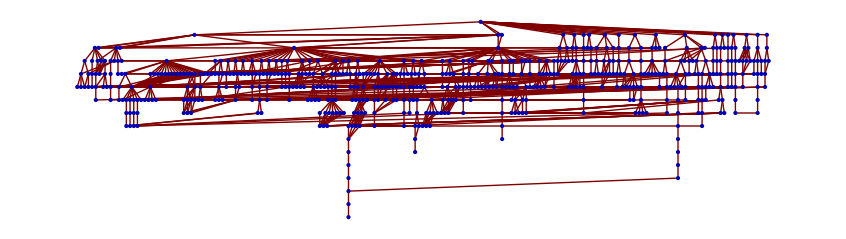

```mathematica
TreePlot[cAllDays,Automatic,"12.129.193.235",VertexLabeling->False,PlotRangePadding->0]
```

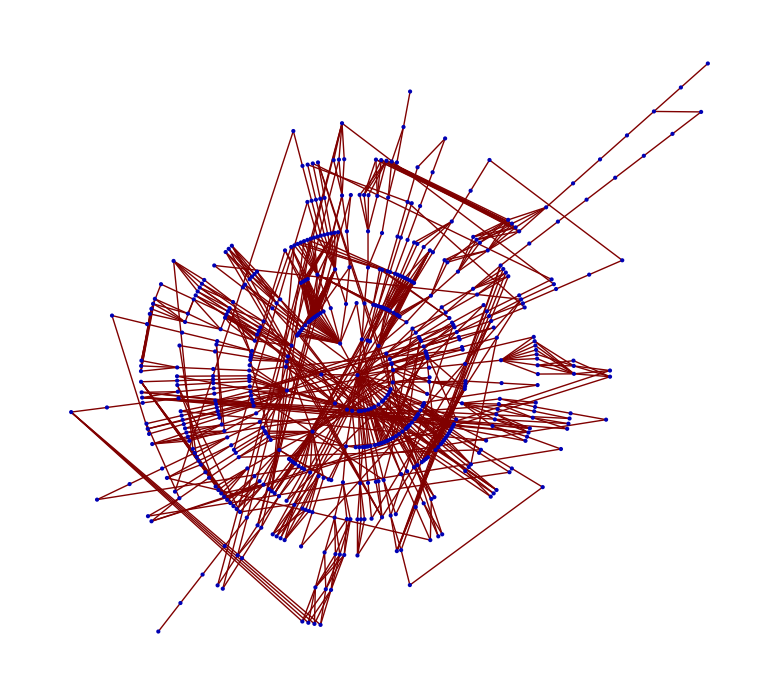

```mathematica
TreePlot[cAllDays,Center,VertexLabeling->False,PlotRangePadding->0]
```

```mathematica
massive = {"12.118.100.21"->"12.122.131.118","12.118.100.22"->"[FW]","12.118.34.30"->"[FW]","12.122.1.2"->"12.122.2.53","12.122.1.209"->"12.122.28.158","12.122.1.210"->"12.122.28.178","12.122.1.5"->"12.122.28.157","12.122.1.6"->"12.122.143.69","12.122.128.101"->"192.205.35.194","12.122.128.105"->"192.205.34.14","12.122.128.13"->"192.205.33.226","12.122.128.14"->"12.123.30.109","12.122.128.170"->"12.123.30.110","12.122.128.2"->"12.123.30.110","12.122.128.2"->"12.123.30.250","12.122.128.25"->"12.122.255.74","12.122.128.25"->"12.129.193.246","12.122.128.26"->"12.123.30.110","12.122.128.6"->"12.123.30.110","12.122.128.6"->"12.123.30.250","12.122.128.9"->"192.205.33.226","12.122.129.10"->"12.123.30.249","12.122.129.101"->"192.205.34.14","12.122.129.106"->"12.123.30.249","12.122.129.13"->"192.205.33.226","12.122.129.170"->"12.123.30.110","12.122.129.170"->"12.123.30.250","12.122.129.2"->"12.123.30.250","12.122.129.25"->"12.122.255.74","12.122.129.25"->"12.129.193.242","12.122.129.25"->"12.129.193.246","12.122.129.26"->"12.123.30.110","12.122.129.26"->"12.123.30.250","12.122.129.29"->"192.205.35.130","12.122.129.6"->"12.123.30.110","12.122.129.6"->"12.123.30.250","12.122.129.61"->"192.205.34.134","12.122.129.9"->"192.205.33.226","12.122.130.125"->"12.118.100.22","12.122.131.118"->"12.122.1.2","12.122.131.118"->"12.122.86.5","12.122.131.22"->"12.122.1.2","12.122.135.10"->"12.122.4.53","12.122.135.129"->"[FW]","12.122.135.14"->"12.122.4.53","12.122.137.150"->"12.122.3.122","12.122.138.22"->"12.122.28.178","12.122.143.69"->"12.88.228.14","12.122.143.70"->"12.122.1.5","12.122.146.77"->"12.118.34.30","12.122.2.125"->"12.122.2.205","12.122.2.126"->"12.122.2.210","12.122.2.205"->"[FW]","12.122.2.205"->"12.122.31.85","12.122.2.206"->"12.122.2.126","12.122.2.209"->"[NR]","12.122.2.209"->"12.122.2.125","12.122.2.210"->"12.122.4.54","12.122.2.53"->"12.122.31.85","12.122.254.41"->"12.122.128.170","12.122.254.41"->"12.122.128.2","12.122.254.41"->"12.122.128.6","12.122.254.41"->"12.122.129.170","12.122.254.41"->"12.122.129.2","12.122.254.65"->"12.122.128.2","12.122.254.65"->"12.122.128.26","12.122.254.65"->"12.122.128.6","12.122.254.65"->"12.122.129.2","12.122.254.65"->"12.122.129.26","12.122.254.65"->"12.122.129.6","12.122.255.69"->"12.122.128.170","12.122.255.69"->"12.122.128.2","12.122.255.69"->"12.122.128.6","12.122.255.69"->"12.122.129.170","12.122.255.69"->"12.122.129.2","12.122.255.73"->"12.122.128.2","12.122.255.73"->"12.122.128.26","12.122.255.73"->"12.122.128.6","12.122.255.73"->"12.122.129.2","12.122.255.73"->"12.122.129.26","12.122.255.73"->"12.122.129.6","12.122.255.74"->"[NR]","12.122.255.74"->"12.129.193.235","12.122.255.74"->"12.129.193.242","12.122.255.74"->"12.129.193.246","12.122.28.157"->"12.122.1.210","12.122.28.158"->"12.122.1.6","12.122.28.177"->"12.122.1.209","12.122.28.178"->"12.123.30.249","12.122.3.122"->"12.123.30.109","12.122.3.37"->"12.122.130.125","12.122.30.25"->"[FW]","12.122.30.25"->"12.122.30.30","12.122.30.25"->"12.123.30.249","12.122.30.26"->"12.122.31.86","12.122.30.29"->"12.122.30.26","12.122.30.30"->"12.122.129.25","12.122.30.30"->"12.123.30.249","12.122.31.134"->"12.122.31.193","12.122.31.193"->"12.122.146.77","12.122.31.85"->"12.122.30.25","12.122.31.85"->"12.122.30.30","12.122.31.86"->"12.122.2.206","12.122.4.53"->"[FW]","12.122.4.53"->"12.122.2.209","12.122.4.54"->"12.122.135.129","12.122.80.226"->"12.122.1.2","12.122.81.18"->"12.122.31.85","12.122.82.222"->"12.122.4.53","12.122.84.201"->"192.205.35.6","12.122.84.201"->"192.205.37.158","12.122.84.202"->"12.123.30.109","12.122.84.202"->"12.123.30.249","12.122.84.217"->"192.205.35.6","12.122.84.217"->"192.205.37.158","12.122.84.218"->"12.122.84.202","12.122.84.218"->"12.123.30.109","12.122.84.46"->"12.122.3.37","12.122.84.50"->"12.122.30.25","12.122.84.50"->"12.122.31.85","12.122.86.5"->"192.205.36.114","12.122.88.174"->"12.122.4.53","12.123.30.109"->"12.122.128.25","12.123.30.109"->"12.122.129.25","12.123.30.109"->"12.122.255.74","12.123.30.110"->"[NR]","12.123.30.110"->"12.122.128.101","12.123.30.110"->"12.122.128.105","12.123.30.110"->"12.122.128.13","12.123.30.110"->"12.122.128.9","12.123.30.110"->"12.122.129.101","12.123.30.110"->"12.122.129.9","12.123.30.110"->"12.122.84.201","12.123.30.110"->"12.122.84.217","12.123.30.110"->"12.123.30.133","12.123.30.110"->"12.123.30.17","12.123.30.110"->"12.123.30.189","12.123.30.110"->"12.123.30.5","12.123.30.133"->"208.174.194.65","12.123.30.17"->"77.67.79.173","12.123.30.189"->"77.67.79.173","12.123.30.249"->"[FW]","12.123.30.249"->"12.122.128.25","12.123.30.249"->"12.122.129.25","12.123.30.249"->"12.122.255.74","12.123.30.250"->"12.122.128.105","12.123.30.250"->"12.122.128.9","12.123.30.250"->"12.122.129.101","12.123.30.250"->"12.122.129.13","12.123.30.250"->"12.122.129.29","12.123.30.250"->"12.122.129.61","12.123.30.250"->"12.122.129.9","12.123.30.250"->"12.122.28.177","12.123.30.250"->"12.122.30.29","12.123.30.250"->"12.122.31.134","12.123.30.250"->"12.122.84.201","12.123.30.250"->"12.122.84.217","12.123.30.250"->"12.123.30.133","12.123.30.250"->"12.123.30.17","12.123.30.250"->"12.123.30.189","12.123.30.250"->"12.123.30.5","12.123.30.5"->"208.174.194.65","12.129.193.235"->"[NR]","12.129.193.235"->"12.129.193.236","12.129.193.235"->"154.11.98.17","12.129.193.235"->"154.11.98.18","12.129.193.235"->"164.128.251.1","12.129.193.235"->"196.25.9.45","12.129.193.235"->"203.202.125.3","12.129.193.235"->"212.241.174.5","12.129.193.235"->"213.192.191.81","12.129.193.235"->"213.200.64.93","12.129.193.235"->"216.113.10.49","12.129.193.235"->"216.18.63.213","12.129.193.235"->"216.191.14.249","12.129.193.235"->"62.48.45.130","12.129.193.235"->"64.135.5.57","12.129.193.235"->"66.162.47.57","12.129.193.235"->"66.209.87.105","12.129.193.235"->"69.31.111.161","12.129.193.235"->"86.55.0.49","12.129.193.236"->"12.129.193.241","12.129.193.236"->"12.129.193.253","12.129.193.241"->"12.122.254.65","12.129.193.241"->"12.122.255.73","12.129.193.242"->"[FW]","12.129.193.242"->"[NR]","12.129.193.242"->"12.129.193.235","12.129.193.242"->"12.129.193.246","12.129.193.246"->"[FW]","12.129.193.246"->"[NR]","12.129.193.246"->"12.129.193.235","12.129.193.253"->"12.122.254.41","12.129.193.253"->"12.122.255.69","12.88.228.13"->"12.122.143.70","12.88.228.14"->"64.135.0.42","130.117.1.73"->"195.66.224.110","130.117.3.226"->"195.66.224.110","130.117.49.105"->"130.117.1.73","130.117.49.105"->"130.117.3.226","130.117.49.93"->"130.117.1.73","130.117.49.93"->"130.117.3.226","130.117.50.89"->"154.54.5.234","130.117.50.90"->"12.122.84.202","130.117.50.90"->"12.122.84.218","130.117.50.90"->"192.205.35.5","130.117.50.90"->"192.205.37.157","138.187.129.100"->"138.187.129.74","138.187.129.105"->"138.187.130.96","138.187.129.110"->"195.66.224.29","138.187.129.137"->"138.187.130.160","138.187.129.193"->"138.187.130.169","138.187.129.74"->"213.200.70.37","138.187.129.74"->"213.248.90.237","138.187.130.160"->"138.187.129.100","138.187.130.160"->"138.187.130.191","138.187.130.160"->"138.187.159.22","138.187.130.160"->"164.128.33.162","138.187.130.161"->"138.187.157.34","138.187.130.169"->"138.187.130.161","138.187.130.180"->"138.187.130.25","138.187.130.180"->"138.187.159.46","138.187.130.181"->"138.187.157.6","138.187.130.191"->"194.68.123.136","138.187.130.24"->"138.187.130.181","138.187.130.25"->"138.187.129.110","138.187.130.96"->"138.187.130.24","138.187.157.33"->"138.187.130.160","138.187.157.34"->"[NR]","138.187.157.34"->"164.128.251.50","138.187.157.5"->"138.187.129.137","138.187.157.5"->"138.187.130.180","138.187.157.6"->"[NR]","138.187.157.6"->"164.128.251.50","138.187.159.21"->"138.187.130.161","138.187.159.22"->"138.187.159.58","138.187.159.22"->"198.32.118.36","138.187.159.22"->"198.32.118.79","138.187.159.22"->"198.32.118.91","138.187.159.22"->"213.248.96.101","138.187.159.45"->"138.187.130.181","138.187.159.46"->"154.11.3.230","138.187.159.46"->"206.223.115.113","138.187.159.46"->"206.223.115.3","138.187.159.46"->"206.223.115.47","138.187.159.57"->"138.187.159.21","138.187.159.58"->"198.32.176.50","144.232.0.24"->"160.81.236.226","144.232.0.26"->"160.81.236.226","144.232.13.43"->"144.232.4.83","144.232.13.50"->"216.113.122.81","144.232.18.123"->"144.232.20.44","144.232.18.123"->"144.232.24.211","144.232.18.123"->"144.232.9.167","144.232.18.209"->"144.232.20.44","144.232.19.100"->"144.232.0.24","144.232.19.100"->"144.232.0.26","144.232.19.146"->"144.232.19.100","144.232.19.146"->"144.232.19.200","144.232.19.181"->"144.232.20.103","144.232.19.200"->"144.232.0.24","144.232.19.200"->"144.232.0.26","144.232.19.235"->"144.232.18.123","144.232.19.235"->"66.110.27.114","144.232.19.237"->"144.232.20.103","144.232.19.245"->"144.232.19.181","144.232.19.245"->"144.232.19.235","144.232.19.245"->"144.232.8.185","144.232.19.245"->"66.110.14.33","144.232.19.245"->"66.110.27.49","144.232.20.103"->"144.232.20.44","144.232.20.103"->"144.232.9.167","144.232.20.103"->"195.219.158.57","144.232.20.103"->"213.206.129.123","144.232.20.143"->"144.232.20.44","144.232.20.163"->"144.232.20.44","144.232.20.166"->"144.232.18.209","144.232.20.166"->"144.232.20.143","144.232.20.166"->"144.232.20.163","144.232.20.166"->"144.232.24.209","144.232.20.44"->"195.219.158.57","144.232.20.44"->"213.206.129.123","144.232.20.44"->"217.118.224.54","144.232.20.44"->"217.147.128.37","144.232.20.74"->"144.232.9.110","144.232.20.96"->"144.232.20.44","144.232.24.13"->"80.77.64.34","144.232.24.209"->"144.232.20.44","144.232.24.211"->"144.232.20.44","144.232.24.211"->"144.232.9.148","144.232.24.211"->"144.232.9.167","144.232.24.50"->"144.232.20.103","144.232.24.50"->"144.232.20.163","144.232.24.50"->"144.232.20.96","144.232.24.50"->"144.232.24.209","144.232.24.66"->"144.232.9.113","144.232.24.66"->"144.232.9.115","144.232.26.11"->"144.232.18.123","144.232.26.11"->"144.232.24.211","144.232.26.11"->"144.232.9.148","144.232.26.11"->"144.232.9.157","144.232.26.69"->"144.232.3.136","144.232.26.69"->"144.232.9.148","144.232.3.136"->"144.232.8.186","144.232.3.139"->"144.232.20.44","144.232.3.213"->"144.232.4.83","144.232.3.213"->"144.232.4.97","144.232.3.213"->"144.232.4.99","144.232.3.215"->"144.232.4.83","144.232.4.83"->"144.232.9.74","144.232.4.83"->"144.232.9.78","144.232.4.85"->"144.232.4.97","144.232.4.87"->"144.232.4.83","144.232.4.89"->"144.232.4.83","144.232.4.91"->"144.232.4.83","144.232.4.91"->"144.232.4.97","144.232.4.97"->"144.232.9.74","144.232.4.97"->"144.232.9.78","144.232.4.99"->"144.232.9.74","144.232.5.100"->"144.232.24.66","144.232.5.102"->"144.232.24.66","144.232.8.185"->"144.232.3.139","144.232.8.185"->"66.110.27.114","144.232.8.186"->"192.205.37.89","144.232.9.110"->"144.232.24.13","144.232.9.113"->"144.232.20.166","144.232.9.113"->"144.232.24.50","144.232.9.115"->"144.232.20.166","144.232.9.115"->"144.232.24.50","144.232.9.148"->"144.232.20.44","144.232.9.148"->"144.232.20.74","144.232.9.148"->"144.232.9.167","144.232.9.148"->"195.219.158.57","144.232.9.157"->"144.232.20.44","144.232.9.157"->"144.232.9.167","144.232.9.166"->"144.232.13.43","144.232.9.166"->"144.232.13.50","144.232.9.166"->"144.232.3.213","144.232.9.166"->"144.232.3.215","144.232.9.166"->"144.232.4.85","144.232.9.166"->"144.232.4.87","144.232.9.166"->"144.232.4.89","144.232.9.166"->"144.232.4.91","144.232.9.167"->"195.219.158.57","144.232.9.167"->"213.206.129.123","144.232.9.167"->"217.118.224.54","144.232.9.167"->"217.147.128.37","144.232.9.74"->"12.122.80.226","144.232.9.78"->"12.122.80.226","149.6.2.193"->"130.117.49.105","149.6.2.193"->"130.117.49.93","152.63.17.2"->"152.63.3.118","152.63.17.2"->"152.63.3.122","152.63.17.2"->"152.63.3.134","152.63.17.2"->"152.63.3.170","152.63.29.198"->"152.63.17.2","152.63.3.118"->"209.58.26.21","152.63.3.122"->"209.58.26.21","152.63.3.134"->"209.58.26.21","152.63.3.170"->"209.58.26.21","154.11.10.150"->"64.86.115.25","154.11.10.186"->"[NR]","154.11.10.186"->"154.11.98.18","154.11.10.190"->"154.11.2.218","154.11.10.217"->"[NR]","154.11.10.217"->"154.11.98.18","154.11.10.230"->"154.11.2.102","154.11.11.142"->"154.11.2.122","154.11.11.142"->"64.127.129.113","154.11.11.142"->"66.192.252.101","154.11.11.142"->"69.31.111.49","154.11.11.178"->"154.11.3.229","154.11.11.246"->"216.113.37.9","154.11.11.30"->"173.182.200.2","154.11.11.30"->"77.67.68.45","154.11.11.70"->"208.175.10.89","154.11.11.98"->"212.184.27.21","154.11.12.201"->"203.208.154.45","154.11.2.102"->"63.218.94.18","154.11.2.122"->"80.91.246.19","154.11.2.122"->"80.91.248.193","154.11.2.122"->"80.91.248.197","154.11.2.122"->"80.91.249.111","154.11.2.205"->"154.11.10.217","154.11.2.218"->"64.230.176.201","154.11.2.53"->"154.11.10.217","154.11.3.213"->"154.11.10.217","154.11.3.217"->"154.11.10.217","154.11.3.229"->"138.187.159.45","154.11.3.230"->"154.11.10.217","154.11.98.17"->"154.11.10.150","154.11.98.17"->"154.11.10.190","154.11.98.17"->"154.11.10.230","154.11.98.17"->"154.11.11.142","154.11.98.17"->"154.11.11.178","154.11.98.17"->"154.11.11.246","154.11.98.17"->"154.11.11.30","154.11.98.17"->"154.11.11.70","154.11.98.17"->"154.11.11.98","154.11.98.17"->"154.11.12.201","154.11.98.17"->"216.191.190.21","154.54.0.174"->"154.11.2.53","154.54.0.205"->"154.54.3.186","154.54.0.205"->"154.54.5.138","154.54.2.229"->"154.54.3.186","154.54.2.229"->"154.54.5.138","154.54.25.209"->"154.54.5.138","154.54.29.21"->"154.54.30.101","154.54.29.21"->"154.54.6.214","154.54.29.21"->"66.28.4.33","154.54.3.138"->"154.54.7.174","154.54.3.186"->"130.117.50.90","154.54.3.186"->"192.205.35.5","154.54.3.194"->"154.54.7.174","154.54.30.101"->"154.54.0.205","154.54.30.101"->"154.54.2.229","154.54.30.193"->"154.54.3.138","154.54.30.197"->"154.54.3.194","154.54.30.197"->"154.54.5.234","154.54.5.1"->"154.54.6.214","154.54.5.1"->"66.28.4.33","154.54.5.138"->"130.117.50.90","154.54.5.138"->"154.54.3.186","154.54.5.234"->"154.54.7.174","154.54.6.201"->"154.54.2.229","154.54.6.209"->"154.54.30.101","154.54.6.209"->"154.54.6.201","154.54.6.209"->"154.54.6.214","154.54.6.209"->"66.28.4.33","154.54.6.214"->"154.54.2.229","154.54.6.214"->"154.54.25.209","154.54.6.229"->"154.54.3.138","154.54.6.229"->"154.54.3.194","154.54.6.229"->"154.54.5.234","154.54.7.174"->"154.54.0.174","154.54.7.174"->"66.28.4.50","157.130.91.249"->"152.63.29.198","160.81.236.226"->"66.192.245.116","164.128.251.1"->"138.187.157.33","164.128.251.1"->"138.187.157.5","164.128.33.162"->"93.63.100.13","164.128.33.162"->"93.63.100.37","164.128.33.162"->"93.63.100.41","164.128.33.162"->"93.63.100.9","164.128.33.169"->"138.187.130.169","164.128.33.209"->"138.187.130.96","166.63.221.193"->"195.2.25.221","166.63.221.193"->"195.2.25.89","166.63.221.194"->"213.192.191.189","173.182.200.2"->"154.54.29.21","173.182.200.2"->"154.54.5.1","173.182.200.2"->"154.54.6.209","192.205.33.225"->"12.122.128.14","192.205.33.225"->"12.122.129.10","192.205.33.226"->"4.69.144.114","192.205.33.226"->"4.69.144.116","192.205.33.226"->"4.69.144.137","192.205.33.226"->"4.69.144.178","192.205.33.226"->"4.69.144.180","192.205.33.226"->"4.69.144.201","192.205.33.226"->"4.69.144.242","192.205.33.226"->"4.69.144.244","192.205.33.226"->"4.69.144.50","192.205.33.226"->"4.69.144.52","192.205.33.226"->"4.69.144.9","192.205.33.229"->"12.122.128.14","192.205.33.229"->"12.122.129.10","192.205.34.134"->"69.31.111.205","192.205.34.14"->"80.91.252.162","192.205.34.209"->"[FW]","192.205.34.209"->"12.122.135.10","192.205.34.209"->"12.122.135.14","192.205.34.53"->"12.122.131.22","192.205.34.77"->"12.122.31.85","192.205.34.77"->"12.122.84.50","192.205.35.130"->"216.6.12.30","192.205.35.194"->"66.192.245.68","192.205.35.5"->"12.122.84.202","192.205.35.5"->"12.122.84.218","192.205.35.5"->"12.123.30.109","192.205.35.5"->"192.205.37.157","192.205.35.6"->"130.117.50.89","192.205.35.6"->"154.54.30.197","192.205.35.6"->"154.54.6.229","192.205.36.114"->"89.149.183.25","192.205.36.121"->"12.122.137.150","192.205.36.137"->"[NR]","192.205.36.137"->"12.122.82.222","192.205.36.137"->"12.122.84.46","192.205.36.205"->"12.122.81.18","192.205.36.241"->"12.122.81.18","192.205.37.157"->"12.122.84.202","192.205.37.157"->"12.122.84.218","192.205.37.157"->"192.205.35.5","192.205.37.158"->"130.117.50.89","192.205.37.158"->"154.54.30.193","192.205.37.158"->"154.54.30.197","192.205.37.158"->"154.54.6.229","192.205.37.89"->"12.122.81.18","192.77.55.12"->"[FW]","193.19.194.133"->"193.19.195.30","193.19.194.133"->"193.19.195.34","193.19.194.134"->"193.19.194.210","193.19.194.134"->"193.19.195.9","193.19.194.209"->"193.19.194.133","193.19.194.210"->"193.19.194.62","193.19.194.210"->"193.19.194.85","193.19.194.210"->"193.19.195.9","193.19.194.61"->"193.19.194.86","193.19.194.61"->"193.19.195.10","193.19.194.62"->"86.55.0.50","193.19.194.85"->"193.19.194.62","193.19.194.86"->"193.19.194.209","193.19.195.10"->"193.19.194.209","193.19.195.29"->"193.19.194.134","193.19.195.29"->"193.19.194.210","193.19.195.30"->"195.16.161.1","193.19.195.30"->"195.66.225.113","193.19.195.30"->"77.67.72.41","193.19.195.30"->"77.67.72.45","193.19.195.30"->"80.81.192.144","193.19.195.30"->"80.81.192.183","193.19.195.30"->"80.81.192.220","193.19.195.30"->"80.81.193.183","193.19.195.33"->"193.19.194.134","193.19.195.34"->"195.16.161.1","193.19.195.34"->"195.66.225.30","193.19.195.34"->"80.81.192.11","193.19.195.34"->"80.81.192.220","193.19.195.44"->"193.19.195.33","193.19.195.46"->"193.19.195.33","193.19.195.50"->"193.19.195.29","193.19.195.50"->"193.19.195.33","193.19.195.52"->"193.19.195.33","193.19.195.54"->"193.19.195.33","193.19.195.9"->"193.19.194.62","193.19.195.9"->"86.55.0.50","193.203.5.14"->"62.72.142.14","193.203.5.14"->"62.72.142.142","193.203.5.216"->"66.216.48.213","193.42.140.17"->"89.97.200.81","193.42.140.17"->"89.97.200.89","193.42.140.4"->"62.48.45.122","194.68.123.136"->"213.192.191.133","195.16.161.1"->"4.68.23.11","195.16.161.1"->"4.68.23.12","195.16.161.1"->"4.68.23.126","195.16.161.1"->"4.68.23.139","195.16.161.1"->"4.68.23.140","195.16.161.1"->"4.68.23.190","195.16.161.1"->"4.68.23.203","195.16.161.1"->"4.68.23.204","195.16.161.1"->"4.68.23.254","195.16.161.1"->"4.68.23.62","195.16.161.1"->"4.68.23.75","195.16.161.1"->"4.68.23.76","195.2.10.109"->"198.32.118.79","195.2.10.110"->"195.2.25.106","195.2.10.110"->"195.2.25.202","195.2.10.110"->"195.2.25.94","195.2.10.110"->"195.2.25.98","195.2.21.138"->"195.2.21.177","195.2.21.177"->"195.2.25.222","195.2.21.177"->"195.2.25.90","195.2.21.197"->"198.32.118.79","195.2.21.198"->"195.2.25.106","195.2.21.198"->"195.2.25.94","195.2.22.65"->"195.2.21.177","195.2.25.101"->"195.2.10.109","195.2.25.101"->"195.2.21.197","195.2.25.102"->"195.2.25.90","195.2.25.105"->"195.2.25.30","195.2.25.106"->"195.2.25.222","195.2.25.106"->"195.2.25.90","195.2.25.18"->"198.32.118.79","195.2.25.197"->"198.32.118.79","195.2.25.201"->"195.2.25.58","195.2.25.202"->"195.2.25.90","195.2.25.21"->"195.2.25.57","195.2.25.221"->"195.2.25.101","195.2.25.221"->"195.2.25.93","195.2.25.222"->"166.63.221.194","195.2.25.30"->"195.2.25.197","195.2.25.57"->"195.2.25.102","195.2.25.57"->"195.2.25.106","195.2.25.58"->"195.2.25.18","195.2.25.58"->"195.2.25.197","195.2.25.89"->"195.2.25.101","195.2.25.89"->"195.2.25.105","195.2.25.89"->"195.2.25.201","195.2.25.89"->"195.2.25.93","195.2.25.89"->"195.2.25.97","195.2.25.90"->"166.63.221.194","195.2.25.93"->"195.2.10.109","195.2.25.93"->"195.2.21.197","195.2.25.94"->"195.2.25.222","195.2.25.94"->"195.2.25.90","195.2.25.97"->"195.2.25.58","195.2.25.98"->"195.2.25.222","195.219.144.10"->"216.6.57.17","195.219.144.10"->"216.6.63.46","195.219.144.10"->"216.6.98.1","195.219.144.9"->"195.219.158.57","195.219.144.98"->"216.6.114.17","195.219.158.57"->"195.219.159.26","195.219.158.57"->"213.206.129.123","195.219.158.57"->"217.147.128.37","195.219.158.58"->"195.219.144.10","195.219.158.58"->"195.219.144.98","195.219.158.58"->"195.219.195.9","195.219.159.25"->"195.219.158.58","195.219.159.26"->"217.147.129.66","195.219.159.26"->"62.48.45.250","195.219.180.97"->"[NR]","195.219.180.97"->"195.219.241.17","195.219.195.10"->"195.219.158.57","195.219.195.9"->"[NR]","195.219.195.9"->"195.219.195.90","195.219.195.90"->"4.68.63.105","195.219.215.85"->"216.6.114.45","195.219.215.85"->"216.6.115.69","195.219.241.110"->"216.6.114.13","195.219.241.110"->"216.6.114.45","195.219.241.110"->"216.6.115.69","195.219.241.114"->"216.6.114.45","195.219.241.114"->"216.6.115.69","195.219.241.17"->"195.219.215.85","195.219.241.17"->"195.219.241.110","195.219.241.17"->"195.219.241.114","195.219.241.17"->"206.82.135.17","195.50.90.201"->"4.69.139.99","195.66.224.110"->"138.187.129.193","195.66.224.114"->"213.192.191.142","195.66.224.29"->"62.72.142.142","195.66.224.37"->"69.22.142.62","195.66.224.76"->"64.125.27.174","195.66.225.101"->"193.19.195.29","195.66.225.101"->"193.19.195.33","195.66.225.113"->"89.167.254.46","195.66.225.30"->"[FW]","195.69.144.54"->"193.19.195.33","195.69.145.122"->"[FW]","196.25.9.45"->"196.43.18.134","196.25.9.45"->"196.43.18.18","196.25.9.45"->"196.43.18.30","196.25.9.45"->"196.43.18.6","196.25.9.45"->"196.43.9.50","196.25.9.45"->"196.43.9.54","196.43.10.86"->"[NR]","196.43.10.86"->"196.25.9.46","196.43.18.134"->"208.49.224.161","196.43.18.134"->"63.218.94.17","196.43.18.18"->"63.218.115.109","196.43.18.30"->"208.49.224.161","196.43.18.30"->"63.218.94.17","196.43.18.6"->"149.6.2.193","196.43.9.50"->"212.113.10.69","196.43.9.50"->"77.67.64.245","196.43.9.54"->"212.113.10.69","196.43.9.54"->"213.155.141.153","196.43.9.54"->"77.67.64.245","198.32.118.36"->"66.192.245.116","198.32.118.52"->"138.187.159.21","198.32.118.68"->"66.216.1.50","198.32.118.79"->"216.113.122.105","198.32.118.91"->"69.22.142.85","198.32.124.130"->"63.218.94.18","198.32.146.49"->"69.22.142.22","198.32.160.137"->"66.216.1.161","198.32.160.41"->"213.192.191.173","198.32.160.78"->"66.59.191.177","198.32.176.129"->"138.187.159.57","198.32.176.187"->"[FW]","198.32.176.20"->"72.52.92.70","198.32.176.22"->"66.59.190.153","198.32.176.50"->"203.208.182.214","198.32.176.50"->"203.208.183.177","198.32.180.61"->"[FW]","198.32.180.65"->"66.59.190.97","199.212.160.102"->"[FW]","199.212.160.102"->"12.118.100.21","199.212.160.102"->"157.130.91.249","199.212.160.102"->"195.66.225.101","199.212.160.102"->"199.212.160.122","199.212.160.102"->"199.212.160.130","199.212.160.106"->"[FW]","199.212.160.114"->"[FW]","199.212.160.121"->"[FW]","199.212.160.122"->"[FW]","199.212.160.125"->"[FW]","199.212.160.130"->"[FW]","199.212.160.14"->"198.32.176.50","199.212.161.14"->"199.212.161.30","199.212.161.154"->"[FW]","199.212.161.194"->"[FW]","199.212.161.198"->"[FW]","199.212.161.202"->"[FW]","199.212.161.30"->"199.212.161.33","199.212.161.33"->"199.212.161.42","199.212.161.42"->"199.212.161.54","199.212.161.50"->"199.212.161.66","199.212.161.54"->"199.212.161.66","199.212.161.66"->"199.212.160.114","199.212.161.66"->"199.212.161.198","203.202.125.3"->"[FW]","203.202.125.3"->"203.208.148.89","203.202.125.3"->"203.208.149.125","203.202.125.3"->"203.208.169.30","203.202.125.3"->"203.208.182.213","203.202.125.3"->"203.208.183.157","203.202.125.3"->"203.208.183.177","203.202.125.3"->"203.208.183.178","203.202.125.3"->"203.208.186.54","203.202.125.3"->"61.88.221.73","203.202.125.3"->"69.22.153.5","203.202.125.3"->"77.67.79.1","203.208.145.82"->"209.58.85.89","203.208.145.82"->"216.6.84.13","203.208.145.82"->"216.6.84.73","203.208.145.94"->"67.16.139.65","203.208.148.162"->"[FW]","203.208.148.17"->"4.78.195.201","203.208.148.18"->"[FW]","203.208.148.206"->"[FW]","203.208.148.214"->"[FW]","203.208.148.86"->"[FW]","203.208.148.89"->"4.79.42.229","203.208.148.89"->"77.67.79.5","203.208.148.90"->"[FW]","203.208.148.94"->"[FW]","203.208.149.125"->"203.208.145.94","203.208.149.166"->"203.208.183.122","203.208.152.118"->"203.208.152.30","203.208.152.30"->"203.208.149.166","203.208.154.45"->"203.208.183.177","203.208.154.46"->"154.11.10.217","203.208.169.157"->"203.208.183.177","203.208.169.29"->"203.208.148.90","203.208.169.30"->"69.22.143.114","203.208.182.213"->"198.32.176.129","203.208.182.213"->"198.32.176.187","203.208.182.213"->"198.32.176.20","203.208.182.213"->"198.32.176.22","203.208.182.213"->"203.208.154.46","203.208.182.214"->"203.208.148.90","203.208.183.122"->"203.208.148.162","203.208.183.122"->"203.208.148.206","203.208.183.122"->"203.208.148.214","203.208.183.122"->"203.208.148.86","203.208.183.122"->"203.208.148.94","203.208.183.157"->"[NR]","203.208.183.157"->"203.208.145.82","203.208.183.157"->"209.58.53.13","203.208.183.157"->"66.192.252.45","203.208.183.177"->"203.208.148.90","203.208.183.177"->"64.208.27.81","203.208.183.178"->"198.32.176.129","203.208.183.178"->"198.32.176.187","203.208.183.178"->"198.32.176.20","203.208.183.178"->"198.32.176.22","203.208.183.178"->"203.208.154.46","203.208.186.53"->"203.208.148.90","203.208.186.54"->"69.22.143.114","204.70.192.101"->"[NR]","204.70.192.101"->"204.70.196.22","204.70.192.101"->"216.113.122.77","204.70.192.121"->"206.24.199.2","204.70.193.146"->"204.70.192.121","204.70.195.114"->"208.175.10.2","204.70.195.129"->"[FW]","204.70.195.129"->"204.70.192.101","204.70.195.133"->"204.70.192.101","204.70.196.22"->"204.70.198.78","204.70.196.22"->"208.173.176.210","204.70.196.22"->"208.174.226.46","204.70.196.241"->"204.70.196.22","204.70.196.245"->"216.113.122.77","204.70.198.5"->"204.70.196.245","204.70.198.78"->"208.173.180.138","204.70.198.9"->"204.70.196.241","204.70.202.29"->"204.70.195.129","204.70.203.121"->"204.70.195.133","206.169.83.1"->"66.192.241.218","206.169.83.1"->"66.192.245.116","206.223.115.113"->"66.59.191.221","206.223.115.147"->"138.187.159.45","206.223.115.3"->"[FW]","206.223.115.3"->"199.212.160.121","206.223.115.3"->"199.212.160.125","206.223.115.36"->"66.192.245.116","206.223.115.47"->"66.216.1.121","206.223.115.47"->"66.216.1.157","206.223.115.61"->"69.22.142.27","206.223.119.113"->"66.59.191.85","206.223.119.18"->"64.127.129.62","206.223.119.18"->"64.127.130.54","206.223.119.3"->"[FW]","206.223.119.36"->"66.192.245.116","206.223.119.37"->"72.52.92.101","206.223.119.48"->"63.218.94.18","206.223.119.61"->"69.31.111.138","206.223.119.82"->"138.187.159.21","206.223.143.122"->"72.52.92.121","206.223.143.63"->"203.208.148.18","206.24.199.2"->"154.11.10.217","206.82.131.14"->"192.205.36.205","206.82.131.14"->"192.205.36.241","206.82.131.14"->"206.82.141.30","206.82.131.14"->"206.82.141.90","206.82.131.14"->"66.110.14.14","206.82.131.14"->"66.110.14.18","206.82.132.30"->"203.208.169.157","206.82.132.30"->"209.58.17.30","206.82.135.14"->"[NR]","206.82.135.14"->"206.82.131.14","206.82.135.14"->"206.82.141.1","206.82.135.14"->"209.58.94.1","206.82.135.17"->"206.82.135.14","206.82.135.17"->"216.6.114.45","206.82.139.5"->"216.6.53.30","206.82.139.98"->"216.6.42.58","206.82.141.1"->"192.205.36.205","206.82.141.1"->"192.205.36.241","206.82.141.1"->"206.82.141.30","206.82.141.1"->"206.82.141.90","206.82.141.1"->"66.110.14.14","206.82.141.1"->"66.110.14.18","206.82.141.30"->"206.82.142.14","206.82.141.90"->"80.91.246.19","206.82.141.90"->"80.91.248.193","206.82.141.90"->"80.91.248.197","206.82.141.90"->"80.91.249.109","206.82.141.90"->"80.91.249.111","206.82.142.10"->"66.198.2.50","206.82.142.10"->"66.198.2.58","206.82.142.14"->"66.192.245.116","207.253.253.138"->"[FW]","207.253.253.138"->"[NR]","207.253.253.138"->"207.96.210.138","207.253.253.159"->"216.113.122.30","207.253.253.160"->"216.113.122.74","207.253.253.160"->"216.113.123.102","207.253.253.160"->"216.113.123.106","207.253.253.160"->"216.113.37.10","207.96.210.138"->"[FW]","207.96.210.138"->"[NR]","207.96.210.159"->"216.113.122.106","207.96.210.159"->"216.113.122.30","207.96.210.159"->"216.113.122.78","207.96.210.160"->"192.77.55.12","207.96.210.160"->"216.113.122.74","207.96.210.160"->"216.113.123.106","208.173.176.210"->"66.59.191.109","208.173.180.138"->"80.91.246.19","208.173.180.138"->"80.91.248.193","208.173.180.138"->"80.91.248.197","208.173.180.138"->"80.91.249.109","208.173.180.138"->"80.91.249.111","208.174.194.65"->"204.70.198.5","208.174.194.65"->"204.70.198.9","208.174.226.46"->"213.200.81.125","208.174.226.46"->"89.149.183.25","208.174.226.46"->"89.149.187.233","208.174.49.1"->"204.70.193.146","208.174.49.69"->"204.70.193.146","208.175.10.2"->"4.68.101.30","208.175.10.2"->"4.68.101.62","208.175.10.89"->"204.70.195.114","208.48.33.106"->"66.192.245.116","208.49.224.161"->"[NR]","208.49.224.161"->"208.48.33.106","208.49.224.161"->"64.212.32.234","208.49.224.162"->"196.43.10.86","209.58.17.30"->"203.208.183.177","209.58.26.21"->"216.6.97.45","209.58.26.21"->"216.6.97.65","209.58.26.21"->"216.6.97.89","209.58.26.65"->"195.219.195.10","209.58.26.65"->"216.6.97.102","209.58.47.13"->"206.82.139.5","209.58.47.13"->"66.198.2.58","209.58.53.13"->"209.58.85.89","209.58.53.13"->"216.6.84.13","209.58.53.13"->"216.6.84.73","209.58.60.133"->"216.6.114.17","209.58.85.89"->"216.6.84.2","209.58.94.1"->"216.6.112.42","209.58.94.2"->"[NR]","209.58.94.2"->"206.82.131.14","209.58.94.2"->"206.82.141.1","209.58.94.34"->"195.219.144.9","209.58.94.9"->"216.6.112.42","209.8.108.61"->"63.218.94.18","209.8.108.62"->"216.113.123.142","209.8.108.65"->"63.218.94.18","212.113.10.69"->"217.163.45.82","212.113.10.69"->"4.69.139.97","212.113.10.70"->"196.43.10.86","212.184.27.185"->"62.154.5.201","212.184.27.186"->"213.192.191.202","212.184.27.21"->"217.239.37.42","212.184.27.22"->"154.11.10.186","212.241.174.1"->"[FW]","212.241.174.5"->"62.72.137.250","212.241.174.5"->"62.72.137.29","212.241.174.5"->"62.72.142.129","212.241.174.5"->"62.72.142.130","212.241.174.5"->"62.72.142.133","213.155.141.153"->"80.91.250.209","213.161.92.182"->"196.43.10.86","213.192.191.133"->"213.192.191.82","213.192.191.134"->"64.214.141.25","213.192.191.141"->"195.66.224.29","213.192.191.141"->"195.66.225.101","213.192.191.142"->"213.192.191.198","213.192.191.173"->"213.192.191.142","213.192.191.174"->"198.32.160.137","213.192.191.174"->"198.32.160.78","213.192.191.189"->"213.192.191.133","213.192.191.190"->"166.63.221.193","213.192.191.197"->"80.81.193.183","213.192.191.198"->"213.192.191.133","213.192.191.201"->"212.184.27.185","213.192.191.201"->"213.200.72.69","213.192.191.201"->"213.242.110.169","213.192.191.202"->"213.192.191.133","213.192.191.225"->"213.192.191.202","213.192.191.226"->"[NR]","213.192.191.226"->"195.69.144.54","213.192.191.226"->"195.69.145.122","213.192.191.81"->"213.192.191.134","213.192.191.81"->"213.192.191.141","213.192.191.81"->"213.192.191.174","213.192.191.81"->"213.192.191.190","213.192.191.81"->"213.192.191.197","213.192.191.81"->"213.192.191.201","213.192.191.81"->"213.192.191.226","213.200.64.93"->"213.200.65.150","213.200.64.93"->"213.200.86.66","213.200.64.93"->"89.149.184.205","213.200.64.93"->"89.149.184.65","213.200.64.93"->"89.149.184.69","213.200.64.93"->"89.149.184.77","213.200.64.93"->"89.149.184.85","213.200.64.93"->"89.149.185.114","213.200.64.93"->"89.149.185.177","213.200.64.93"->"89.149.185.193","213.200.64.93"->"89.149.185.198","213.200.64.93"->"89.149.185.218","213.200.64.93"->"89.149.185.222","213.200.64.93"->"89.149.185.46","213.200.64.93"->"89.149.185.77","213.200.64.93"->"89.149.185.81","213.200.64.93"->"89.149.185.89","213.200.64.93"->"89.149.186.145","213.200.64.93"->"89.149.186.181","213.200.64.93"->"89.149.186.201","213.200.64.93"->"89.149.186.34","213.200.64.93"->"89.149.186.37","213.200.64.93"->"89.149.187.214","213.200.64.93"->"89.149.187.218","213.200.65.150"->"69.31.111.205","213.200.66.185"->"213.200.81.98","213.200.66.185"->"213.200.82.5","213.200.66.185"->"89.149.186.142","213.200.66.57"->"213.200.64.94","213.200.66.57"->"213.200.81.125","213.200.66.57"->"89.149.183.25","213.200.66.57"->"89.149.187.233","213.200.68.153"->"89.149.184.10","213.200.68.153"->"89.149.184.117","213.200.68.153"->"89.149.184.205","213.200.68.153"->"89.149.185.193","213.200.68.153"->"89.149.185.89","213.200.68.153"->"89.149.186.169","213.200.68.153"->"89.149.186.201","213.200.68.153"->"89.149.186.69","213.200.68.153"->"89.149.187.214","213.200.68.153"->"89.149.187.218","213.200.68.154"->"62.48.45.250","213.200.70.37"->"89.149.184.10","213.200.70.37"->"89.149.185.193","213.200.70.37"->"89.149.186.169","213.200.70.37"->"89.149.186.69","213.200.70.37"->"89.149.187.214","213.200.70.37"->"89.149.187.218","213.200.72.69"->"213.200.82.14","213.200.72.69"->"213.200.82.30","213.200.72.69"->"213.200.82.86","213.200.72.69"->"89.149.184.53","213.200.72.69"->"89.149.185.161","213.200.72.69"->"89.149.185.237","213.200.72.69"->"89.149.185.61","213.200.72.69"->"89.149.186.22","213.200.72.70"->"213.192.191.202","213.200.77.129"->"89.149.184.78","213.200.77.129"->"89.149.184.86","213.200.77.129"->"89.149.186.182","213.200.77.129"->"89.149.186.38","213.200.78.237"->"213.200.82.30","213.200.78.237"->"89.149.185.161","213.200.80.197"->"213.200.82.5","213.200.80.197"->"89.149.186.142","213.200.81.125"->"213.200.64.94","213.200.81.98"->"213.200.68.154","213.200.82.14"->"213.200.64.94","213.200.82.30"->"213.200.68.154","213.200.82.5"->"213.200.64.94","213.200.82.86"->"213.200.64.94","213.200.86.66"->"[NR]","213.200.86.66"->"195.219.241.17","213.206.129.122"->"144.232.9.166","213.206.129.123"->"195.219.159.26","213.206.129.123"->"217.147.128.37","213.206.129.123"->"217.147.129.66","213.206.129.124"->"217.147.96.75","213.206.129.124"->"217.147.96.77","213.206.129.125"->"80.93.8.43","213.206.129.126"->"80.93.8.42","213.206.129.127"->"217.147.128.41","213.206.129.34"->"80.77.96.100","213.206.129.57"->"213.206.129.34","213.206.129.62"->"213.206.129.57","213.206.129.65"->"144.232.19.146","213.206.131.58"->"80.91.254.250","213.242.110.169"->"4.69.140.198","213.242.110.170"->"213.192.191.202","213.248.100.93"->"80.91.250.225","213.248.100.93"->"80.91.250.229","213.248.100.94"->"[FW]","213.248.100.94"->"[NR]","213.248.100.94"->"212.241.174.1","213.248.100.94"->"62.72.142.14","213.248.100.94"->"62.72.142.142","213.248.65.117"->"80.91.247.241","213.248.65.209"->"213.248.100.94","213.248.65.209"->"80.91.250.230","213.248.65.209"->"80.91.251.206","213.248.65.210"->"192.205.34.209","213.248.65.210"->"213.248.88.46","213.248.65.89"->"80.91.250.226","213.248.65.93"->"80.91.250.226","213.248.65.93"->"80.91.250.230","213.248.65.97"->"80.91.250.230","213.248.65.98"->"192.205.34.209","213.248.77.50"->"154.11.10.217","213.248.80.145"->"80.91.248.138","213.248.80.145"->"80.91.252.217","213.248.80.148"->"80.91.246.19","213.248.80.148"->"80.91.248.193","213.248.82.14"->"213.248.77.50","213.248.82.238"->"196.43.10.86","213.248.88.46"->"66.192.245.116","213.248.90.237"->"80.91.249.115","213.248.91.162"->"204.70.203.121","213.248.96.101"->"192.205.34.53","213.248.96.82"->"204.70.202.29","216.113.10.49"->"207.253.253.159","216.113.10.49"->"207.253.253.160","216.113.10.49"->"207.96.210.159","216.113.10.49"->"207.96.210.160","216.113.122.105"->"207.253.253.138","216.113.122.105"->"207.96.210.138","216.113.122.106"->"198.32.118.52","216.113.122.106"->"198.32.118.68","216.113.122.29"->"[FW]","216.113.122.29"->"[NR]","216.113.122.29"->"207.253.253.138","216.113.122.29"->"207.96.210.138","216.113.122.30"->"216.113.122.62","216.113.122.30"->"216.113.122.90","216.113.122.30"->"216.113.123.141","216.113.122.62"->"[NR]","216.113.122.62"->"209.8.108.61","216.113.122.62"->"216.66.77.113","216.113.122.74"->"144.232.26.11","216.113.122.74"->"144.232.26.69","216.113.122.77"->"207.253.253.138","216.113.122.78"->"204.70.195.114","216.113.122.78"->"204.70.196.22","216.113.122.81"->"207.96.210.138","216.113.122.89"->"207.96.210.138","216.113.122.89"->"216.113.122.29","216.113.122.90"->"216.6.115.70","216.113.123.102"->"216.113.122.106","216.113.123.105"->"207.96.210.138","216.113.123.106"->"216.113.122.62","216.113.123.106"->"66.59.191.157","216.113.123.141"->"69.31.111.37","216.113.123.142"->"216.113.122.29","216.113.123.142"->"216.113.123.105","216.113.125.85"->"207.253.253.138","216.113.125.85"->"207.96.210.138","216.113.125.85"->"216.113.122.29","216.113.37.10"->"154.11.10.217","216.113.37.9"->"207.96.210.138","216.18.63.197"->"66.59.191.26","216.18.63.197"->"66.59.191.38","216.18.63.198"->"66.59.191.210","216.18.63.213"->"66.59.191.25","216.18.63.213"->"66.59.191.33","216.18.63.213"->"66.59.191.37","216.191.14.249"->"154.11.3.217","216.191.14.249"->"199.212.160.102","216.191.14.249"->"199.212.160.14","216.191.14.249"->"199.212.161.154","216.191.14.249"->"199.212.161.202","216.191.14.249"->"216.191.190.30","216.191.14.249"->"66.59.191.133","216.191.190.21"->"[FW]","216.191.190.30"->"207.253.253.138","216.191.65.93"->"[FW]","216.6.112.41"->"209.58.94.2","216.6.112.41"->"209.58.94.34","216.6.112.42"->"66.59.191.149","216.6.114.13"->"216.113.125.85","216.6.114.17"->"216.113.125.85","216.6.114.17"->"216.6.114.2","216.6.114.2"->"216.6.115.58","216.6.114.45"->"216.113.122.89","216.6.114.45"->"216.113.125.85","216.6.115.21"->"216.113.122.89","216.6.115.58"->"154.11.10.186","216.6.115.69"->"216.113.125.85","216.6.115.70"->"206.82.135.14","216.6.12.30"->"216.6.63.45","216.6.12.30"->"216.6.63.5","216.6.42.58"->"195.219.195.10","216.6.42.58"->"216.6.97.102","216.6.53.30"->"209.58.26.65","216.6.53.30"->"216.6.42.58","216.6.53.30"->"216.6.97.45","216.6.53.30"->"216.6.97.89","216.6.53.58"->"209.58.60.133","216.6.53.70"->"[NR]","216.6.53.70"->"66.198.2.2","216.6.53.81"->"216.6.53.70","216.6.57.17"->"216.6.57.82","216.6.57.18"->"195.219.144.9","216.6.57.58"->"216.6.115.21","216.6.57.82"->"216.6.53.81","216.6.63.45"->"195.219.144.9","216.6.63.46"->"206.82.132.30","216.6.63.5"->"195.219.144.9","216.6.84.13"->"216.6.84.2","216.6.84.2"->"216.6.57.18","216.6.84.2"->"216.6.57.58","216.6.84.73"->"216.6.84.2","216.6.97.102"->"195.219.158.57","216.6.97.45"->"195.219.195.10","216.6.97.45"->"216.6.97.102","216.6.97.65"->"216.6.97.102","216.6.97.89"->"195.219.195.10","216.6.97.89"->"216.6.97.102","216.6.98.1"->"209.58.94.9","216.6.98.2"->"195.219.144.9","216.6.98.29"->"216.6.98.2","216.66.77.113"->"72.52.92.101","217.118.224.54"->"213.206.129.123","217.118.224.54"->"217.147.128.37","217.147.128.37"->"213.206.129.123","217.147.128.37"->"217.147.129.66","217.147.128.37"->"62.48.45.250","217.147.128.37"->"62.48.45.253","217.147.128.38"->"213.206.129.122","217.147.128.41"->"217.147.129.66","217.147.128.42"->"213.206.129.126","217.147.129.65"->"217.147.128.38","217.147.129.65"->"217.147.128.42","217.147.129.66"->"[NR]","217.147.129.66"->"62.48.45.129","217.147.129.66"->"62.48.45.253","217.147.96.34"->"213.206.129.65","217.147.96.74"->"213.206.129.125","217.147.96.75"->"213.206.129.62","217.147.96.75"->"4.68.111.141","217.147.96.75"->"64.215.195.209","217.147.96.77"->"213.206.131.58","217.163.45.82"->"62.72.142.142","217.239.37.42"->"212.184.27.186","4.53.84.222"->"[FW]","4.68.101.30"->"4.69.140.190","4.68.101.62"->"4.69.140.194","4.68.111.101"->"4.68.23.14","4.68.111.101"->"4.68.23.206","4.68.111.101"->"4.68.23.78","4.68.111.141"->"4.68.23.126","4.68.111.141"->"4.68.23.190","4.68.111.141"->"4.68.23.254","4.68.111.141"->"4.68.23.62","4.68.111.142"->"217.147.96.34","4.68.111.142"->"217.147.96.74","4.68.111.146"->"195.219.241.17","4.68.111.170"->"144.232.5.100","4.68.111.170"->"144.232.5.102","4.68.111.90"->"144.232.5.100","4.68.111.90"->"144.232.5.102","4.68.16.137"->"4.78.179.6","4.68.16.137"->"64.152.45.198","4.68.16.196"->"4.53.84.222","4.68.16.201"->"64.152.45.198","4.68.16.4"->"4.53.84.222","4.68.16.68"->"4.53.84.222","4.68.16.73"->"64.152.45.198","4.68.16.9"->"64.152.45.198","4.68.17.146"->"4.68.62.26","4.68.17.146"->"4.68.62.34","4.68.17.18"->"4.68.62.30","4.68.17.18"->"4.68.62.34","4.68.17.210"->"4.68.62.26","4.68.17.210"->"4.68.62.30","4.68.17.82"->"4.68.62.26","4.68.17.82"->"4.68.62.30","4.68.18.132"->"4.79.42.230","4.68.18.190"->"4.69.134.249","4.68.18.196"->"4.79.42.230","4.68.18.4"->"4.79.42.230","4.68.18.68"->"4.79.42.230","4.68.23.11"->"4.68.111.142","4.68.23.12"->"195.219.180.97","4.68.23.12"->"4.68.111.146","4.68.23.126"->"4.69.140.17","4.68.23.126"->"4.69.140.21","4.68.23.126"->"4.69.140.25","4.68.23.126"->"4.69.140.29","4.68.23.139"->"4.68.111.142","4.68.23.14"->"193.19.195.50","4.68.23.140"->"195.219.180.97","4.68.23.140"->"4.68.111.146","4.68.23.142"->"193.19.195.50","4.68.23.190"->"4.69.140.17","4.68.23.190"->"4.69.140.21","4.68.23.190"->"4.69.140.25","4.68.23.190"->"4.69.140.29","4.68.23.203"->"4.68.111.142","4.68.23.204"->"195.219.180.97","4.68.23.204"->"4.68.111.146","4.68.23.206"->"193.19.195.50","4.68.23.254"->"4.69.140.17","4.68.23.254"->"4.69.140.21","4.68.23.254"->"4.69.140.25","4.68.23.254"->"4.69.140.29","4.68.23.62"->"4.69.140.17","4.68.23.62"->"4.69.140.21","4.68.23.62"->"4.69.140.29","4.68.23.75"->"4.68.111.142","4.68.23.76"->"195.219.180.97","4.68.23.76"->"4.68.111.146","4.68.23.78"->"193.19.195.50","4.68.62.26"->"12.122.88.174","4.68.62.30"->"12.122.88.174","4.68.62.34"->"12.122.88.174","4.68.63.105"->"4.69.139.97","4.68.63.121"->"4.68.23.142","4.68.63.121"->"4.68.23.206","4.68.63.121"->"4.68.23.78","4.69.132.113"->"4.69.132.61","4.69.132.114"->"4.69.132.70","4.69.132.134"->"4.69.141.169","4.69.132.137"->"4.69.141.150","4.69.132.137"->"4.69.142.169","4.69.132.138"->"4.69.137.50","4.69.132.138"->"4.69.137.54","4.69.132.138"->"4.69.137.58","4.69.132.138"->"4.69.137.62","4.69.132.138"->"4.69.140.22","4.69.132.138"->"4.69.140.26","4.69.132.138"->"4.69.140.30","4.69.132.37"->"4.69.132.57","4.69.132.37"->"4.69.133.125","4.69.132.38"->"4.69.132.62","4.69.132.57"->"4.69.134.210","4.69.132.57"->"4.69.134.214","4.69.132.57"->"4.69.134.218","4.69.132.57"->"4.69.134.222","4.69.132.61"->"4.69.132.37","4.69.132.62"->"4.69.132.114","4.69.132.69"->"4.69.132.113","4.69.132.70"->"4.69.134.146","4.69.132.70"->"4.69.134.150","4.69.132.70"->"4.69.134.154","4.69.132.70"->"4.69.134.158","4.69.132.70"->"4.69.137.49","4.69.132.70"->"4.69.137.53","4.69.132.70"->"4.69.137.57","4.69.132.70"->"4.69.137.61","4.69.132.82"->"4.69.134.178","4.69.132.82"->"4.69.134.182","4.69.132.82"->"4.69.134.186","4.69.132.9"->"[NR]","4.69.132.9"->"4.69.134.226","4.69.132.9"->"4.69.134.230","4.69.132.9"->"4.69.134.234","4.69.132.9"->"4.69.134.238","4.69.132.93"->"4.69.134.178","4.69.132.93"->"4.69.134.182","4.69.132.93"->"4.69.134.186","4.69.132.93"->"4.69.134.190","4.69.132.94"->"4.69.134.66","4.69.132.94"->"4.69.134.70","4.69.132.94"->"4.69.134.74","4.69.132.94"->"4.69.134.78","4.69.132.94"->"4.69.137.65","4.69.132.94"->"4.69.137.69","4.69.132.94"->"4.69.137.73","4.69.132.94"->"4.69.137.77","4.69.133.109"->"4.71.176.6","4.69.133.110"->"4.69.144.10","4.69.133.110"->"4.69.144.135","4.69.133.110"->"4.69.144.138","4.69.133.110"->"4.69.144.199","4.69.133.110"->"4.69.144.202","4.69.133.110"->"4.69.144.7","4.69.133.110"->"4.69.144.71","4.69.133.110"->"4.69.144.74","4.69.133.113"->"4.71.176.6","4.69.133.114"->"4.69.133.118","4.69.133.117"->"4.69.133.113","4.69.133.118"->"4.69.133.122","4.69.133.121"->"4.69.133.117","4.69.133.122"->"4.69.133.126","4.69.133.125"->"4.69.133.121","4.69.133.126"->"4.69.132.38","4.69.133.89"->"4.69.139.138","4.69.133.90"->"4.69.141.149","4.69.134.114"->"4.68.16.137","4.69.134.114"->"4.68.16.73","4.69.134.114"->"4.69.134.73","4.69.134.114"->"4.69.134.77","4.69.134.117"->"4.69.135.185","4.69.134.118"->"4.68.16.137","4.69.134.118"->"4.68.16.201","4.69.134.118"->"4.69.134.69","4.69.134.121"->"4.69.135.185","4.69.134.122"->"4.68.16.137","4.69.134.122"->"4.69.134.65","4.69.134.122"->"4.69.134.69","4.69.134.122"->"4.69.134.73","4.69.134.125"->"4.69.135.185","4.69.134.126"->"4.68.16.137","4.69.134.126"->"4.68.16.73","4.69.134.126"->"4.68.16.9","4.69.134.126"->"4.69.134.65","4.69.134.126"->"4.69.134.73","4.69.134.126"->"4.69.134.77","4.69.134.145"->"4.69.132.69","4.69.134.145"->"4.69.137.49","4.69.134.145"->"4.69.137.53","4.69.134.145"->"4.69.137.57","4.69.134.145"->"4.69.137.61","4.69.134.146"->"4.69.134.181","4.69.134.146"->"4.69.134.185","4.69.134.146"->"4.69.134.189","4.69.134.149"->"4.69.132.69","4.69.134.149"->"4.69.137.57","4.69.134.149"->"4.69.137.61","4.69.134.150"->"4.68.17.146","4.69.134.150"->"4.68.17.18","4.69.134.150"->"4.68.17.210","4.69.134.150"->"4.68.17.82","4.69.134.150"->"4.69.134.177","4.69.134.150"->"4.69.134.181","4.69.134.150"->"4.69.134.185","4.69.134.150"->"4.69.134.189","4.69.134.153"->"4.69.132.69","4.69.134.153"->"4.69.137.49","4.69.134.153"->"4.69.137.53","4.69.134.153"->"4.69.137.61","4.69.134.154"->"4.68.17.146","4.69.134.154"->"4.68.17.18","4.69.134.154"->"4.68.17.82","4.69.134.154"->"4.69.134.177","4.69.134.154"->"4.69.134.189","4.69.134.157"->"4.69.132.69","4.69.134.157"->"4.69.137.53","4.69.134.157"->"4.69.137.57","4.69.134.157"->"4.69.137.61","4.69.134.158"->"4.68.17.18","4.69.134.158"->"4.68.17.210","4.69.134.158"->"4.68.17.82","4.69.134.158"->"4.69.134.177","4.69.134.158"->"4.69.134.181","4.69.134.158"->"4.69.134.185","4.69.134.158"->"4.69.134.189","4.69.134.177"->"4.69.132.94","4.69.134.178"->"4.69.134.145","4.69.134.178"->"4.69.134.149","4.69.134.178"->"4.69.134.153","4.69.134.178"->"4.69.134.157","4.69.134.181"->"4.69.132.94","4.69.134.182"->"4.69.134.145","4.69.134.182"->"4.69.134.149","4.69.134.182"->"4.69.134.153","4.69.134.185"->"4.69.132.94","4.69.134.186"->"4.69.134.145","4.69.134.186"->"4.69.134.149","4.69.134.186"->"4.69.134.153","4.69.134.189"->"4.69.132.94","4.69.134.190"->"4.69.134.149","4.69.134.210"->"4.68.18.196","4.69.134.214"->"4.68.18.4","4.69.134.218"->"4.68.18.68","4.69.134.222"->"4.68.18.132","4.69.134.226"->"4.68.18.4","4.69.134.226"->"4.69.134.249","4.69.134.226"->"4.69.134.253","4.69.134.230"->"4.68.18.4","4.69.134.230"->"4.68.18.68","4.69.134.230"->"4.69.134.241","4.69.134.230"->"4.69.134.249","4.69.134.230"->"4.69.134.253","4.69.134.234"->"4.68.18.196","4.69.134.234"->"4.68.18.68","4.69.134.234"->"4.69.134.241","4.69.134.234"->"4.69.134.253","4.69.134.238"->"4.68.18.132","4.69.134.238"->"4.69.134.241","4.69.134.238"->"4.69.134.253","4.69.134.241"->"4.69.135.186","4.69.134.242"->"4.68.18.196","4.69.134.242"->"4.68.18.4","4.69.134.246"->"4.68.18.4","4.69.134.246"->"4.68.18.68","4.69.134.249"->"4.69.135.186","4.69.134.250"->"4.68.18.68","4.69.134.253"->"4.69.135.186","4.69.134.254"->"4.68.18.132","4.69.134.65"->"4.69.137.69","4.69.134.65"->"4.69.137.77","4.69.134.66"->"4.68.16.4","4.69.134.66"->"4.68.16.68","4.69.134.66"->"4.69.134.121","4.69.134.69"->"4.69.137.65","4.69.134.69"->"4.69.137.69","4.69.134.69"->"4.69.137.73","4.69.134.69"->"4.69.137.77","4.69.134.70"->"4.68.16.4","4.69.134.70"->"4.68.16.68","4.69.134.70"->"4.69.134.121","4.69.134.70"->"4.69.134.125","4.69.134.73"->"4.69.137.65","4.69.134.73"->"4.69.137.69","4.69.134.73"->"4.69.137.73","4.69.134.73"->"4.69.137.77","4.69.134.74"->"4.68.16.196","4.69.134.74"->"4.68.16.68","4.69.134.74"->"4.69.134.117","4.69.134.77"->"4.69.137.69","4.69.134.78"->"4.68.16.196","4.69.134.78"->"4.68.16.4","4.69.134.78"->"4.69.134.117","4.69.135.185"->"4.69.134.242","4.69.135.185"->"4.69.134.246","4.69.135.185"->"4.69.134.250","4.69.135.185"->"4.69.134.254","4.69.135.186"->"4.69.134.114","4.69.135.186"->"4.69.134.118","4.69.135.186"->"4.69.134.122","4.69.135.186"->"4.69.134.126","4.69.137.49"->"4.69.132.137","4.69.137.49"->"4.69.140.18","4.69.137.49"->"4.69.140.22","4.69.137.49"->"4.69.140.30","4.69.137.50"->"4.69.134.146","4.69.137.50"->"4.69.134.150","4.69.137.50"->"4.69.134.154","4.69.137.50"->"4.69.134.158","4.69.137.53"->"4.69.132.137","4.69.137.53"->"4.69.140.18","4.69.137.53"->"4.69.140.26","4.69.137.53"->"4.69.140.30","4.69.137.54"->"4.69.134.146","4.69.137.54"->"4.69.134.150","4.69.137.54"->"4.69.134.154","4.69.137.54"->"4.69.134.158","4.69.137.57"->"4.69.132.137","4.69.137.57"->"4.69.140.18","4.69.137.57"->"4.69.140.22","4.69.137.57"->"4.69.140.26","4.69.137.57"->"4.69.140.30","4.69.137.58"->"4.69.134.150","4.69.137.58"->"4.69.134.154","4.69.137.58"->"4.69.134.158","4.69.137.61"->"4.69.132.137","4.69.137.61"->"4.69.140.18","4.69.137.61"->"4.69.140.26","4.69.137.62"->"4.69.134.150","4.69.137.62"->"4.69.134.158","4.69.137.65"->"4.69.139.102","4.69.137.66"->"4.69.132.93","4.69.137.69"->"4.69.139.102","4.69.137.70"->"4.69.132.93","4.69.137.73"->"4.69.139.102","4.69.137.74"->"4.69.132.93","4.69.137.77"->"4.69.139.102","4.69.137.78"->"4.69.132.93","4.69.139.102"->"212.113.10.70","4.69.139.102"->"217.163.45.82","4.69.139.138"->"208.174.49.1","4.69.139.138"->"208.174.49.69","4.69.139.97"->"4.69.132.134","4.69.139.97"->"4.69.137.66","4.69.139.97"->"4.69.137.70","4.69.139.97"->"4.69.137.74","4.69.139.97"->"4.69.137.78","4.69.139.99"->"213.200.77.129","4.69.140.17"->"4.69.132.137","4.69.140.17"->"4.69.137.50","4.69.140.17"->"4.69.137.54","4.69.140.17"->"4.69.137.58","4.69.140.18"->"4.68.23.14","4.69.140.18"->"4.68.23.142","4.69.140.18"->"4.68.23.206","4.69.140.18"->"4.68.23.78","4.69.140.190"->"4.69.132.61","4.69.140.194"->"4.69.132.70","4.69.140.197"->"213.242.110.170","4.69.140.198"->"4.69.142.170","4.69.140.21"->"4.69.132.137","4.69.140.21"->"4.69.137.50","4.69.140.21"->"4.69.137.54","4.69.140.21"->"4.69.137.58","4.69.140.21"->"4.69.137.62","4.69.140.22"->"4.68.23.14","4.69.140.22"->"4.68.23.78","4.69.140.25"->"4.69.137.50","4.69.140.25"->"4.69.137.54","4.69.140.25"->"4.69.137.58","4.69.140.26"->"4.68.23.14","4.69.140.26"->"4.68.23.142","4.69.140.26"->"4.68.23.206","4.69.140.26"->"4.68.23.78","4.69.140.29"->"4.69.132.137","4.69.140.29"->"4.69.137.50","4.69.140.29"->"4.69.137.54","4.69.140.29"->"4.69.137.58","4.69.140.29"->"4.69.137.62","4.69.140.30"->"4.68.23.14","4.69.140.30"->"4.68.23.142","4.69.140.30"->"4.68.23.206","4.69.140.30"->"4.68.23.78","4.69.141.149"->"4.69.132.138","4.69.141.149"->"4.69.142.169","4.69.141.150"->"4.69.133.89","4.69.141.169"->"4.69.133.90","4.69.142.169"->"4.69.140.197","4.69.142.170"->"4.69.132.138","4.69.144.10"->"4.68.111.90","4.69.144.114"->"4.69.133.109","4.69.144.116"->"4.69.132.82","4.69.144.116"->"4.69.132.9","4.69.144.135"->"192.205.33.225","4.69.144.137"->"4.78.195.202","4.69.144.138"->"4.68.111.90","4.69.144.178"->"4.69.133.109","4.69.144.180"->"4.69.132.82","4.69.144.180"->"4.69.132.9","4.69.144.199"->"192.205.33.225","4.69.144.201"->"4.78.195.202","4.69.144.202"->"4.68.111.90","4.69.144.242"->"4.69.133.109","4.69.144.244"->"4.69.132.82","4.69.144.244"->"4.69.132.9","4.69.144.50"->"4.69.133.109","4.69.144.52"->"4.69.132.82","4.69.144.52"->"4.69.132.9","4.69.144.7"->"192.205.33.229","4.69.144.71"->"192.205.33.225","4.69.144.71"->"192.205.33.229","4.69.144.74"->"4.68.111.170","4.69.144.74"->"4.68.111.90","4.69.144.9"->"4.78.195.202","4.71.176.5"->"4.69.133.110","4.71.176.5"->"4.69.133.114","4.71.176.6"->"66.209.64.194","4.78.179.6"->"[FW]","4.78.195.201"->"4.69.144.199","4.78.195.201"->"4.69.144.7","4.78.195.201"->"4.69.144.71","4.78.195.202"->"203.208.148.18","4.79.42.229"->"4.68.18.190","4.79.42.230"->"203.208.148.90","61.88.221.73"->"203.208.148.17","62.154.5.201"->"212.184.27.22","62.48.45.122"->"[NR]","62.48.45.122"->"62.48.45.129","62.48.45.123"->"193.42.140.17","62.48.45.130"->"62.48.45.123","62.48.45.130"->"62.48.45.251","62.48.45.130"->"62.48.45.252","62.48.45.250"->"[NR]","62.48.45.250"->"217.147.129.66","62.48.45.250"->"62.48.45.129","62.48.45.251"->"195.219.159.25","62.48.45.251"->"213.200.68.153","62.48.45.252"->"217.147.129.65","62.48.45.253"->"[NR]","62.48.45.253"->"62.48.45.129","62.72.137.250"->"195.69.145.122","62.72.137.29"->"195.66.224.110","62.72.137.29"->"195.66.224.114","62.72.137.29"->"195.66.224.37","62.72.137.29"->"195.66.224.76","62.72.137.29"->"195.66.225.101","62.72.142.129"->"213.248.100.93","62.72.142.130"->"195.50.90.201","62.72.142.133"->"193.203.5.216","62.72.142.14"->"[FW]","62.72.142.14"->"[NR]","62.72.142.142"->"[FW]","62.72.142.142"->"212.241.174.1","63.218.115.109"->"63.218.252.106","63.218.252.106"->"203.208.152.118","63.218.94.17"->"[NR]","63.218.94.17"->"154.11.3.213","63.218.94.17"->"206.223.115.113","63.218.94.17"->"206.223.115.3","63.218.94.17"->"206.223.115.47","63.218.94.17"->"209.8.108.62","63.218.94.17"->"63.218.94.2","63.218.94.17"->"69.31.30.9","63.218.94.18"->"196.43.10.86","63.218.94.2"->"72.52.92.85","64.125.27.153"->"213.161.92.182","64.125.27.157"->"213.161.92.182","64.125.27.174"->"64.125.27.153","64.125.27.174"->"64.125.27.157","64.127.128.145"->"206.223.143.63","64.127.128.145"->"66.186.192.22","64.127.128.146"->"64.127.128.237","64.127.128.237"->"64.127.130.49","64.127.128.238"->"[NR]","64.127.128.238"->"64.127.128.145","64.127.129.113"->"64.127.129.62","64.127.129.113"->"64.127.130.54","64.127.129.114"->"154.11.10.217","64.127.129.61"->"64.127.129.114","64.127.129.62"->"66.186.192.197","64.127.130.49"->"64.127.130.57","64.127.130.50"->"64.127.128.238","64.127.130.54"->"64.127.130.57","64.127.130.57"->"66.216.1.141","64.127.130.57"->"66.216.1.158","64.127.130.57"->"66.216.1.254","64.127.130.58"->"64.127.130.50","64.128.212.33"->"66.192.245.116","64.132.69.221"->"66.192.245.116","64.135.0.42"->"64.135.0.5","64.135.0.43"->"12.88.228.13","64.135.0.5"->"[NR]","64.135.0.5"->"64.135.5.58","64.135.0.6"->"64.135.0.43","64.135.5.57"->"64.135.0.6","64.135.5.57"->"66.216.1.93","64.152.45.198"->"[FW]","64.208.27.81"->"64.214.141.26","64.208.27.81"->"67.17.109.213","64.212.32.234"->"66.192.250.114","64.214.141.25"->"208.48.33.106","64.214.141.25"->"69.31.111.205","64.214.141.26"->"213.192.191.133","64.215.195.209"->"69.31.110.237","64.215.195.209"->"69.31.111.205","64.230.158.26"->"67.69.199.126","64.230.176.177"->"64.230.158.26","64.230.176.201"->"64.230.176.177","64.86.115.25"->"216.6.98.29","66.110.14.14"->"89.149.183.25","66.110.14.18"->"213.200.81.125","66.110.14.18"->"89.149.183.25","66.110.14.18"->"89.149.187.233","66.110.14.33"->"144.232.18.123","66.110.14.33"->"144.232.9.148","66.110.27.114"->"144.232.20.103","66.110.27.114"->"144.232.20.44","66.110.27.114"->"144.232.9.148","66.110.27.45"->"66.110.27.114","66.110.27.49"->"144.232.20.103","66.110.27.49"->"144.232.24.211","66.110.27.49"->"144.232.3.139","66.110.27.9"->"144.232.19.237","66.110.27.9"->"66.110.27.45","66.162.47.57"->"66.192.240.94","66.162.47.57"->"66.192.243.138","66.162.47.57"->"66.192.243.234","66.162.47.57"->"66.192.243.98","66.162.47.57"->"66.192.244.20","66.162.47.57"->"66.192.246.53","66.162.47.57"->"66.192.250.114","66.162.47.57"->"66.192.250.254","66.162.47.57"->"66.192.253.26","66.186.192.197"->"66.186.192.46","66.186.192.198"->"64.127.129.61","66.186.192.198"->"66.186.192.202","66.186.192.202"->"198.32.180.61","66.186.192.202"->"198.32.180.65","66.186.192.21"->"[FW]","66.186.192.21"->"198.32.146.49","66.186.192.21"->"206.223.143.122","66.186.192.21"->"206.223.143.63","66.186.192.21"->"213.200.80.197","66.186.192.21"->"64.127.128.146","66.186.192.22"->"66.186.192.46","66.186.192.45"->"66.186.192.198","66.186.192.45"->"66.186.192.21","66.186.192.46"->"66.209.64.194","66.192.240.94"->"12.122.138.22","66.192.240.94"->"138.187.159.21","66.192.240.94"->"206.82.142.10","66.192.240.94"->"209.58.47.13","66.192.240.94"->"213.200.82.5","66.192.240.94"->"213.248.80.145","66.192.240.94"->"213.248.80.148","66.192.240.94"->"64.127.130.49","66.192.240.94"->"66.198.2.1","66.192.240.94"->"66.198.2.37","66.192.240.94"->"69.22.142.2","66.192.240.94"->"72.52.92.62","66.192.240.94"->"80.91.248.208","66.192.240.94"->"80.91.248.214","66.192.240.94"->"80.91.252.62","66.192.240.94"->"89.149.186.142","66.192.241.218"->"12.122.129.106","66.192.241.218"->"213.200.81.98","66.192.243.138"->"[FW]","66.192.243.234"->"195.2.10.110","66.192.243.234"->"195.2.21.138","66.192.243.234"->"195.2.21.198","66.192.243.234"->"195.2.25.21","66.192.243.98"->"154.11.10.217","66.192.243.98"->"203.208.148.90","66.192.243.98"->"66.59.190.153","66.192.244.20"->"[FW]","66.192.245.116"->"[NR]","66.192.245.116"->"66.162.47.58","66.192.245.68"->"[NR]","66.192.245.68"->"66.162.47.58","66.192.246.53"->"12.122.138.22","66.192.246.53"->"138.187.159.21","66.192.246.53"->"206.82.142.10","66.192.246.53"->"209.58.47.13","66.192.246.53"->"213.200.82.5","66.192.246.53"->"213.248.80.148","66.192.246.53"->"64.127.130.49","66.192.246.53"->"66.198.2.1","66.192.246.53"->"66.198.2.37","66.192.246.53"->"69.22.142.2","66.192.246.53"->"72.52.92.62","66.192.246.53"->"80.91.248.208","66.192.246.53"->"80.91.248.214","66.192.246.53"->"89.149.186.142","66.192.250.114"->"66.209.64.154","66.192.250.114"->"66.209.64.161","66.192.250.254"->"66.209.64.154","66.192.250.254"->"66.209.64.161","66.192.252.101"->"66.192.245.116","66.192.252.45"->"66.192.245.68","66.192.253.26"->"154.11.10.217","66.192.253.26"->"203.208.148.90","66.192.253.26"->"66.59.190.153","66.198.2.1"->"206.82.139.5","66.198.2.1"->"66.198.2.50","66.198.2.1"->"66.198.2.58","66.198.2.2"->"206.82.142.14","66.198.2.37"->"66.198.2.50","66.198.2.37"->"66.198.2.58","66.198.2.50"->"216.6.53.58","66.198.2.58"->"206.82.139.98","66.198.2.58"->"216.6.53.30","66.209.64.153"->"206.169.83.1","66.209.64.154"->"66.209.64.181","66.209.64.161"->"66.209.64.194","66.209.64.162"->"206.169.83.1","66.209.64.181"->"[NR]","66.209.64.181"->"66.209.87.106","66.209.64.182"->"66.209.64.153","66.209.64.193"->"4.71.176.5","66.209.64.193"->"66.186.192.45","66.209.64.193"->"66.209.64.162","66.209.64.194"->"[NR]","66.209.64.194"->"66.209.87.106","66.209.87.105"->"66.209.64.182","66.209.87.105"->"66.209.64.193","66.216.1.121"->"66.216.1.126","66.216.1.122"->"206.223.115.113","66.216.1.122"->"206.223.115.147","66.216.1.122"->"206.223.115.3","66.216.1.122"->"206.223.115.36","66.216.1.122"->"206.223.115.61","66.216.1.122"->"213.200.66.185","66.216.1.122"->"66.216.1.162","66.216.1.122"->"66.216.1.2","66.216.1.122"->"66.216.1.49","66.216.1.126"->"64.135.0.42","66.216.1.141"->"206.223.115.147","66.216.1.141"->"66.216.1.162","66.216.1.142"->"64.127.130.58","66.216.1.157"->"64.127.130.58","66.216.1.158"->"66.216.1.162","66.216.1.158"->"66.216.1.49","66.216.1.161"->"66.216.1.121","66.216.1.161"->"66.216.1.142","66.216.1.161"->"66.216.1.157","66.216.1.162"->"198.32.160.41","66.216.1.162"->"66.216.48.214","66.216.1.2"->"154.11.10.217","66.216.1.245"->"198.32.124.130","66.216.1.245"->"66.216.1.122","66.216.1.253"->"64.127.130.58","66.216.1.254"->"66.216.1.94","66.216.1.49"->"198.32.118.79","66.216.1.50"->"66.216.1.121","66.216.1.50"->"66.216.1.142","66.216.1.93"->"66.216.1.245","66.216.1.93"->"66.216.1.253","66.216.1.94"->"[NR]","66.216.1.94"->"64.135.5.58","66.216.48.213"->"66.216.1.161","66.216.48.214"->"[NR]","66.216.48.214"->"193.203.5.14","66.216.48.214"->"195.66.224.29","66.216.48.214"->"80.81.192.107","66.216.48.217"->"[NR]","66.216.48.217"->"66.216.1.50","66.28.4.33"->"154.54.0.205","66.28.4.33"->"154.54.2.229","66.28.4.50"->"154.11.2.53","66.59.190.153"->"66.59.190.97","66.59.190.154"->"198.32.176.50","66.59.190.50"->"66.59.190.154","66.59.190.61"->"66.59.191.34","66.59.190.61"->"66.59.191.38","66.59.190.62"->"66.59.190.50","66.59.190.97"->"66.59.190.61","66.59.191.109"->"66.59.191.34","66.59.191.110"->"206.223.119.18","66.59.191.110"->"206.223.119.48","66.59.191.133"->"66.59.191.141","66.59.191.141"->"216.18.63.197","66.59.191.142"->"66.59.191.158","66.59.191.149"->"66.59.191.26","66.59.191.149"->"66.59.191.34","66.59.191.149"->"66.59.191.38","66.59.191.150"->"216.191.65.93","66.59.191.150"->"216.6.112.41","66.59.191.150"->"67.69.199.121","66.59.191.157"->"66.59.191.141","66.59.191.158"->"216.113.122.29","66.59.191.177"->"216.18.63.197","66.59.191.177"->"66.59.191.230","66.59.191.209"->"66.59.191.230","66.59.191.210"->"198.32.160.41","66.59.191.221"->"66.59.191.177","66.59.191.221"->"66.59.191.209","66.59.191.229"->"66.59.191.142","66.59.191.230"->"66.59.191.34","66.59.191.25"->"216.18.63.198","66.59.191.25"->"66.59.190.62","66.59.191.25"->"66.59.191.110","66.59.191.25"->"66.59.191.150","66.59.191.25"->"66.59.191.86","66.59.191.26"->"[FW]","66.59.191.33"->"66.59.191.150","66.59.191.33"->"66.59.191.229","66.59.191.33"->"66.59.191.86","66.59.191.34"->"[FW]","66.59.191.37"->"66.59.191.110","66.59.191.37"->"66.59.191.150","66.59.191.38"->"[FW]","66.59.191.85"->"66.59.191.34","66.59.191.86"->"206.223.119.18","66.59.191.86"->"206.223.119.36","66.59.191.86"->"206.223.119.37","66.59.191.86"->"206.223.119.61","66.59.191.86"->"206.223.119.82","67.16.139.65"->"208.49.224.162","67.17.106.245"->"192.205.34.77","67.17.106.246"->"213.200.66.57","67.17.106.246"->"213.200.81.125","67.17.106.246"->"89.149.183.25","67.17.109.118"->"213.200.81.125","67.17.109.213"->"64.214.141.26","67.69.199.121"->"67.69.246.150","67.69.199.126"->"66.59.191.149","67.69.246.150"->"154.11.10.186","69.22.142.101"->"69.31.111.134","69.22.142.102"->"69.22.142.97","69.22.142.2"->"69.31.111.138","69.22.142.22"->"69.22.142.2","69.22.142.26"->"69.31.31.186","69.22.142.27"->"69.31.111.134","69.22.142.62"->"69.22.142.85","69.22.142.63"->"195.66.224.29","69.22.142.85"->"69.31.111.138","69.22.142.86"->"198.32.118.52","69.22.142.86"->"69.22.142.63","69.22.142.96"->"69.22.142.101","69.22.142.97"->"69.22.143.113","69.22.143.113"->"203.208.169.29","69.22.143.113"->"203.208.186.53","69.22.143.113"->"69.22.153.6","69.22.143.114"->"69.22.142.96","69.22.153.5"->"69.22.143.114","69.22.153.6"->"203.208.148.90","69.31.110.225"->"144.232.19.245","69.31.110.225"->"192.205.34.77","69.31.110.225"->"213.200.66.57","69.31.110.225"->"66.110.27.9","69.31.110.225"->"67.17.106.246","69.31.110.233"->"144.232.19.245","69.31.110.233"->"192.205.34.77","69.31.110.233"->"213.200.66.57","69.31.110.233"->"67.17.106.245","69.31.110.237"->"69.31.111.134","69.31.111.110"->"72.52.92.101","69.31.111.114"->"63.218.94.18","69.31.111.133"->"69.22.142.102","69.31.111.133"->"69.22.142.26","69.31.111.133"->"69.31.110.225","69.31.111.133"->"69.31.110.233","69.31.111.133"->"69.31.111.201","69.31.111.134"->"69.31.111.255","69.31.111.137"->"206.223.119.48","69.31.111.137"->"209.8.108.65","69.31.111.137"->"69.22.142.86","69.31.111.137"->"69.31.110.225","69.31.111.137"->"69.31.110.233","69.31.111.137"->"69.31.111.110","69.31.111.137"->"69.31.111.114","69.31.111.137"->"69.31.111.201","69.31.111.138"->"69.31.111.255","69.31.111.161"->"154.11.2.205","69.31.111.161"->"206.223.119.113","69.31.111.161"->"206.223.119.18","69.31.111.161"->"206.223.119.3","69.31.111.161"->"206.223.119.36","69.31.111.161"->"69.31.111.133","69.31.111.161"->"69.31.111.137","69.31.111.161"->"69.31.111.38","69.31.111.161"->"69.31.111.42","69.31.111.161"->"69.31.111.50","69.31.111.201"->"144.232.19.245","69.31.111.201"->"213.200.66.57","69.31.111.201"->"67.17.106.245","69.31.111.201"->"67.17.106.246","69.31.111.201"->"67.17.109.118","69.31.111.205"->"69.31.111.134","69.31.111.37"->"69.31.111.255","69.31.111.38"->"216.113.123.142","69.31.111.42"->"216.113.123.142","69.31.111.49"->"69.31.111.255","69.31.111.50"->"154.11.10.217","69.31.30.9"->"69.22.142.27","69.31.31.186"->"195.2.22.65","72.52.92.101"->"72.52.92.242","72.52.92.101"->"72.52.92.34","72.52.92.101"->"72.52.92.78","72.52.92.121"->"72.52.92.225","72.52.92.225"->"72.52.92.78","72.52.92.242"->"72.52.92.34","72.52.92.26"->"72.52.92.101","72.52.92.26"->"72.52.92.242","72.52.92.34"->"[NR]","72.52.92.34"->"72.52.92.90","72.52.92.62"->"72.52.92.85","72.52.92.70"->"72.52.92.26","72.52.92.70"->"72.52.92.74","72.52.92.74"->"72.52.92.101","72.52.92.74"->"72.52.92.242","72.52.92.74"->"72.52.92.78","72.52.92.78"->"72.52.92.34","72.52.92.78"->"72.52.92.90","72.52.92.85"->"72.52.92.242","72.52.92.85"->"72.52.92.78","72.52.92.90"->"[FW]","72.52.92.90"->"[NR]","72.52.92.90"->"193.19.195.29","72.52.92.90"->"80.81.192.107","77.67.64.245"->"213.200.82.30","77.67.64.245"->"89.149.184.78","77.67.64.245"->"89.149.184.86","77.67.64.245"->"89.149.186.182","77.67.64.245"->"89.149.186.38","77.67.64.246"->"196.43.10.86","77.67.66.210"->"66.216.48.217","77.67.67.194"->"80.91.247.188","77.67.67.194"->"80.91.247.190","77.67.68.42"->"154.11.10.217","77.67.68.45"->"213.200.82.5","77.67.68.45"->"89.149.186.142","77.67.72.14"->"80.91.251.121","77.67.72.14"->"80.91.251.123","77.67.72.14"->"80.91.251.125","77.67.72.41"->"89.149.184.66","77.67.72.41"->"89.149.184.70","77.67.72.41"->"89.149.185.17","77.67.72.41"->"89.149.185.5","77.67.72.45"->"89.149.184.66","77.67.72.45"->"89.149.184.70","77.67.79.1"->"213.200.81.125","77.67.79.1"->"89.149.187.233","77.67.79.14"->"203.208.148.18","77.67.79.173"->"[NR]","77.67.79.173"->"213.200.82.5","77.67.79.173"->"89.149.186.142","77.67.79.250"->"154.11.10.217","77.67.79.5"->"89.149.187.182","77.67.79.5"->"89.149.187.186","77.67.79.6"->"203.208.148.90","80.239.193.246"->"66.192.245.116","80.77.64.34"->"213.206.129.34","80.77.96.100"->"80.77.97.22","80.77.96.100"->"80.77.97.54","80.77.97.22"->"213.192.191.202","80.77.97.54"->"213.192.191.202","80.81.192.107"->"193.19.194.134","80.81.192.107"->"193.19.195.29","80.81.192.107"->"193.19.195.33","80.81.192.11"->"62.72.142.14","80.81.192.11"->"62.72.142.142","80.81.192.144"->"213.192.191.198","80.81.192.183"->"138.187.129.105","80.81.192.220"->"66.216.48.213","80.81.193.183"->"138.187.130.96","80.91.246.19"->"213.248.65.89","80.91.246.19"->"80.91.248.253","80.91.246.19"->"80.91.249.16","80.91.246.19"->"80.91.249.248","80.91.246.19"->"80.91.253.117","80.91.247.172"->"213.248.65.209","80.91.247.172"->"80.91.251.208","80.91.247.188"->"80.91.252.233","80.91.247.189"->"4.68.63.121","80.91.247.190"->"80.91.248.61","80.91.247.190"->"80.91.248.65","80.91.247.241"->"80.91.250.226","80.91.247.241"->"80.91.250.230","80.91.247.255"->"80.91.250.226","80.91.247.35"->"80.91.250.226","80.91.247.38"->"80.91.247.255","80.91.247.38"->"80.91.247.35","80.91.247.38"->"80.91.254.208","80.91.247.79"->"4.68.111.101","80.91.247.88"->"213.200.78.237","80.91.247.91"->"80.91.251.209","80.91.248.138"->"213.248.65.97","80.91.248.138"->"80.91.247.172","80.91.248.138"->"80.91.252.217","80.91.248.158"->"213.248.82.238","80.91.248.193"->"213.248.65.89","80.91.248.193"->"213.248.65.93","80.91.248.193"->"80.91.248.253","80.91.248.193"->"80.91.249.16","80.91.248.193"->"80.91.249.248","80.91.248.193"->"80.91.250.146","80.91.248.193"->"80.91.253.106","80.91.248.197"->"213.248.65.93","80.91.248.197"->"80.91.248.158","80.91.248.197"->"80.91.249.16","80.91.248.197"->"80.91.249.248","80.91.248.197"->"80.91.250.146","80.91.248.208"->"80.91.248.193","80.91.248.208"->"80.91.248.197","80.91.248.208"->"80.91.249.109","80.91.248.208"->"80.91.249.111","80.91.248.214"->"80.91.248.138","80.91.248.214"->"80.91.251.28","80.91.248.214"->"80.91.252.57","80.91.248.253"->"80.91.250.226","80.91.248.253"->"80.91.250.230","80.91.248.61"->"80.91.247.241","80.91.248.65"->"80.91.247.241","80.91.248.69"->"80.91.247.241","80.91.248.69"->"80.91.247.255","80.91.248.69"->"80.91.247.35","80.91.248.89"->"213.248.91.162","80.91.248.89"->"213.248.96.82","80.91.249.109"->"213.248.65.93","80.91.249.109"->"80.91.249.248","80.91.249.109"->"80.91.250.146","80.91.249.111"->"213.248.65.93","80.91.249.111"->"80.91.248.158","80.91.249.111"->"80.91.248.253","80.91.249.111"->"80.91.249.16","80.91.249.111"->"80.91.249.248","80.91.249.115"->"80.91.247.189","80.91.249.115"->"80.91.247.79","80.91.249.115"->"80.91.251.124","80.91.249.115"->"80.91.251.126","80.91.249.115"->"80.91.251.250","80.91.249.16"->"213.248.82.238","80.91.249.176"->"213.200.78.237","80.91.249.179"->"213.248.65.210","80.91.249.181"->"213.248.65.210","80.91.249.181"->"80.91.251.207","80.91.249.248"->"[NR]","80.91.249.248"->"80.91.250.226","80.91.249.248"->"80.91.250.230","80.91.249.249"->"213.248.82.14","80.91.249.45"->"80.91.247.241","80.91.249.45"->"80.91.247.255","80.91.249.45"->"80.91.254.208","80.91.250.146"->"213.248.82.238","80.91.250.169"->"213.248.65.210","80.91.250.169"->"80.91.251.207","80.91.250.209"->"80.91.247.91","80.91.250.209"->"80.91.249.179","80.91.250.209"->"80.91.249.181","80.91.250.209"->"80.91.250.169","80.91.250.209"->"80.91.252.197","80.91.250.209"->"80.91.252.205","80.91.250.209"->"80.91.252.209","80.91.250.225"->"80.91.248.89","80.91.250.225"->"80.91.249.249","80.91.250.225"->"80.91.251.207","80.91.250.226"->"213.248.100.94","80.91.250.226"->"62.72.142.142","80.91.250.229"->"213.248.65.210","80.91.250.229"->"80.91.247.88","80.91.250.229"->"80.91.249.176","80.91.250.230"->"213.248.100.94","80.91.251.121"->"80.91.248.69","80.91.251.123"->"213.248.65.117","80.91.251.123"->"80.91.252.229","80.91.251.123"->"80.91.254.205","80.91.251.124"->"4.68.63.121","80.91.251.125"->"80.91.249.45","80.91.251.126"->"4.68.63.121","80.91.251.206"->"213.248.100.94","80.91.251.206"->"213.248.65.209","80.91.251.206"->"80.91.251.208","80.91.251.207"->"192.205.34.209","80.91.251.207"->"213.248.88.46","80.91.251.207"->"80.239.193.246","80.91.251.208"->"213.248.100.94","80.91.251.208"->"80.91.250.226","80.91.251.209"->"192.205.34.209","80.91.251.210"->"80.91.247.35","80.91.251.250"->"4.68.111.101","80.91.251.250"->"4.68.63.121","80.91.251.28"->"213.248.65.209","80.91.252.162"->"213.248.65.89","80.91.252.162"->"80.91.249.248","80.91.252.197"->"213.248.65.98","80.91.252.197"->"80.91.251.209","80.91.252.205"->"80.91.251.207","80.91.252.205"->"80.91.251.209","80.91.252.209"->"213.248.65.98","80.91.252.217"->"213.248.65.97","80.91.252.217"->"80.91.247.172","80.91.252.217"->"80.91.250.226","80.91.252.217"->"80.91.250.230","80.91.252.217"->"80.91.251.206","80.91.252.229"->"80.91.247.241","80.91.252.229"->"80.91.254.208","80.91.252.233"->"80.91.247.241","80.91.252.57"->"213.248.65.209","80.91.252.62"->"80.91.252.217","80.91.253.106"->"213.248.82.238","80.91.253.117"->"80.91.250.226","80.91.254.205"->"80.91.247.35","80.91.254.205"->"80.91.254.208","80.91.254.208"->"80.91.250.226","80.91.254.250"->"80.91.247.38","80.91.254.250"->"80.91.248.69","80.91.254.250"->"80.91.249.45","80.91.254.250"->"80.91.251.210","80.91.254.250"->"80.91.252.229","80.91.254.250"->"80.91.254.205","80.93.8.42"->"213.206.129.124","80.93.8.43"->"213.206.129.127","86.55.0.49"->"193.19.194.61","86.55.0.50"->"213.192.191.81","86.55.0.50"->"216.113.10.49","89.149.183.25"->"213.200.64.94","89.149.183.25"->"213.200.81.125","89.149.184.10"->"[NR]","89.149.184.10"->"213.200.64.94","89.149.184.117"->"[NR]","89.149.184.117"->"213.200.64.94","89.149.184.205"->"77.67.66.210","89.149.184.53"->"77.67.79.6","89.149.184.65"->"193.19.195.44","89.149.184.65"->"193.19.195.46","89.149.184.65"->"77.67.72.14","89.149.184.66"->"213.200.64.94","89.149.184.66"->"213.200.65.150","89.149.184.69"->"193.19.195.46","89.149.184.69"->"193.19.195.52","89.149.184.69"->"193.19.195.54","89.149.184.69"->"77.67.67.194","89.149.184.69"->"77.67.72.14","89.149.184.70"->"213.200.64.94","89.149.184.70"->"213.200.65.150","89.149.184.77"->"164.128.33.209","89.149.184.78"->"[NR]","89.149.184.78"->"213.200.64.94","89.149.184.85"->"164.128.33.209","89.149.184.86"->"213.200.64.94","89.149.185.114"->"192.205.36.137","89.149.185.114"->"64.128.212.33","89.149.185.114"->"64.132.69.221","89.149.185.161"->"77.67.79.6","89.149.185.17"->"192.205.36.137","89.149.185.177"->"77.67.79.14","89.149.185.193"->"77.67.64.246","89.149.185.198"->"192.205.36.137","89.149.185.198"->"64.128.212.33","89.149.185.198"->"64.132.69.221","89.149.185.218"->"77.67.79.14","89.149.185.222"->"77.67.79.14","89.149.185.237"->"77.67.64.246","89.149.185.46"->"77.67.68.42","89.149.185.46"->"77.67.79.250","89.149.185.5"->"192.205.36.137","89.149.185.61"->"213.200.64.94","89.149.185.77"->"77.67.68.42","89.149.185.77"->"77.67.79.250","89.149.185.81"->"77.67.68.42","89.149.185.81"->"77.67.79.250","89.149.185.89"->"77.67.66.210","89.149.186.142"->"213.200.64.94","89.149.186.145"->"213.200.68.154","89.149.186.169"->"213.200.64.94","89.149.186.181"->"164.128.33.209","89.149.186.182"->"213.200.64.94","89.149.186.201"->"77.67.66.210","89.149.186.22"->"77.67.64.246","89.149.186.34"->"213.200.72.70","89.149.186.37"->"164.128.33.209","89.149.186.38"->"213.200.64.94","89.149.186.69"->"[NR]","89.149.186.69"->"213.200.64.94","89.149.187.182"->"192.205.36.121","89.149.187.186"->"192.205.36.121","89.149.187.214"->"77.67.64.246","89.149.187.218"->"77.67.64.246","89.149.187.233"->"213.200.64.94","89.167.254.46"->"196.43.10.86","89.96.200.1"->"89.96.200.110","89.96.200.1"->"89.96.200.18","89.96.200.110"->"164.128.33.169","89.96.200.114"->"164.128.33.169","89.96.200.18"->"164.128.33.169","89.96.200.21"->"164.128.33.169","89.96.200.5"->"89.96.200.110","89.96.200.5"->"89.96.200.18","89.97.200.245"->"89.97.200.83","89.97.200.245"->"89.97.200.91","89.97.200.250"->"89.96.200.114","89.97.200.250"->"89.96.200.21","89.97.200.254"->"89.96.200.114","89.97.200.81"->"89.96.200.1","89.97.200.81"->"89.96.200.5","89.97.200.83"->"193.42.140.4","89.97.200.89"->"89.97.200.250","89.97.200.89"->"89.97.200.254","89.97.200.91"->"193.42.140.4","93.63.100.13"->"89.97.200.245","93.63.100.18"->"89.97.200.83","93.63.100.18"->"89.97.200.91","93.63.100.37"->"93.63.100.18","93.63.100.41"->"89.97.200.245","93.63.100.41"->"93.63.100.18","93.63.100.9"->"89.97.200.245"};
```

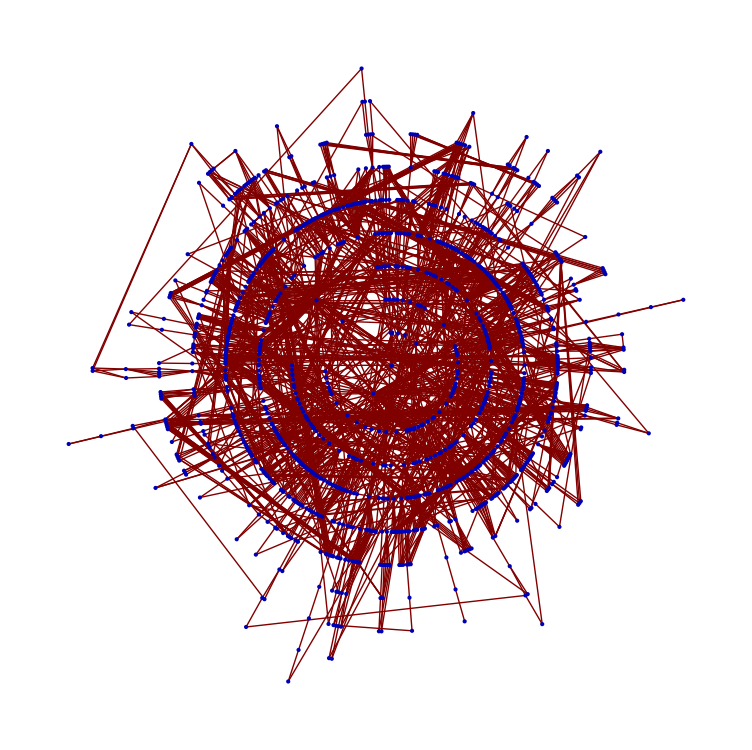

```mathematica
TreePlot[massive,Center,VertexLabeling->False,PlotRangePadding->0]
```